## 1. Initialization and Symbol Definition

## 1.1 - Package and Clear Variables

```mathematica
(*Import FeynCalc Package*)
```

```mathematica
<<FeynCalc`
```

FeynCalc is already loaded! If you are trying to reload FeynCalc or load FeynArts, TARCER, PHI, FeynHelpers or any other add-on, please restart the kernel.

$Aborted

```mathematica
(*Clear Variables and Scalar Products*)
```

```mathematica
ClearAll["Global`*"];
ClearScalarProducts;
```

## 1.2 - Tensor Symbol Definition

```mathematica
(*Compton Tensor*)
```

```mathematica
ϵt[a_,b_]:=(Sqrt[2]*Eps[LorentzIndex[a],LorentzIndex[b],Momentum[q],Momentum[qp]])/(-Sqrt[Contract[Eps[LorentzIndex[a],LorentzIndex[b],Momentum[q],Momentum[qp]]*Eps[LorentzIndex[a],LorentzIndex[b],Momentum[q],Momentum[qp]]]]);
gt[a_,b_]:=Contract[ϵt[a,c]*ϵt[b,c]];

𝒯1[a_,b_]:=-1/2 gt[a,b];
𝒯1t[a_,b_]:=ⅈ/2 ϵt[a,b];

(*Twist-3 pieces*)

𝒯2[a_,b_,c_]:=-1/(SP[p,q]+SP[pp,q]) ((FV[q,b]-SP[q,q]/SP[q,qp] FV[qp,b])*gt[a,c]);

𝒯2t[a_,b_,c_]:=ⅈ/(SP[p,q]+SP[pp,q]) ((FV[q,b]-SP[q,q]/SP[q,qp] FV[qp,b])*ϵt[a,c]);
```

```mathematica
(*Polarization Vector*)
```

```mathematica
SL[μ_]:=M/(1+ξ)(-FV[n,μ]+SP[n,p]/M^2 FV[p,μ]);
STin[μ_]:=1/((1+ξ)Sqrt[-4M^2ξ^2-t(1-ξ^2)])(Contract[Eps[LorentzIndex[μ],LorentzIndex[ν],Momentum[p],Momentum[n]]*Eps[Momentum[n],Momentum[p],Momentum[pp],LorentzIndex[ν]]]);
STout[μ_]:=1/Sqrt[-4M^2ξ^2-t(1-ξ^2)] Eps[Momentum[n],Momentum[p],Momentum[pp],LorentzIndex[μ]];
```

## 1.3 - Leptonic Tensor

```mathematica
(*DVCS Leptonic Tensor*)
```

```mathematica
(LDVCSunp=Simplify[DiracSimplify[1/2*FermionSpinSum[ComplexConjugate[SpinorUBar[kp].(GA[α1]/Q^2).SpinorU[k]]*SpinorUBar[kp].(GA[α2]/Q^2).SpinorU[k]]],{h^2==1}]) //TraditionalForm
(LDVCSp=Simplify[-ⅈ*DiracSimplify[1/2*FermionSpinSum[ComplexConjugate[SpinorUBar[kp].(GA[α1]/Q^2).SpinorU[k]]*SpinorUBar[kp].(GA[α2]/Q^2).DiracMatrix[5].SpinorU[k]]],{h^2==1}]) //TraditionalForm
```

(2 (-(ḡ)^α1α2 (k̄·OverBar[kp])+(k̄)^α2 OverBar[kp]^α1+(k̄)^α1 OverBar[kp]^α2))/Q^4

(2 (ϵ̄)^(α1α2 k̄ OverBar[kp]))/Q^4

```mathematica
(*Interference Leptonic Tensor*)
```

```mathematica
(LINTunp=Expand[Simplify[DiracSimplify[1/2*FermionSpinSum[ComplexConjugate[SpinorUBar[kp].GA[α2].SpinorU[k]]*Contract[SpinorUBar[kp].(GA[α1].((GS[kp]+GS[qp])/(2 SP[kp,qp])).GA[α]+GA[α].((GS[k]-GS[qp])/(-2SP[k,qp])).GA[α1]).SpinorU[k]]]]]]) //TraditionalForm;
(LINTp=Expand[Simplify[-ⅈ*DiracSimplify[1/2*FermionSpinSum[ComplexConjugate[SpinorUBar[kp].GA[α2].SpinorU[k]]*Contract[SpinorUBar[kp].(GA[α1].((GS[kp]+GS[qp])/(2 SP[kp,qp])).GA[α]+GA[α].((GS[k]-GS[qp])/(-2SP[k,qp])).GA[α1]).DiracMatrix[5].SpinorU[k]]]]]]) //TraditionalForm;
```

## 2. Scalar Coefficient

## 2.1 - DVCS Scalar Coefficients (Twist-2 and Twist-3)

```mathematica
(*DVCS Twist-2 Scalar Coefficients*)
```

```mathematica
(hampc=Simplify[ScalarProductExpand[Contract[(Q^4*LDVCSunp/.{Momentum[kp]->Momentum[k]-Momentum[q]})*ComplexConjugate[𝒯1[α3,α1]]*𝒯1[α4,α2]*(-MT[α3,α4])]]]) //TraditionalForm
(htampc=Simplify[ScalarProductExpand[Contract[(Q^4*LDVCSunp/.{Momentum[kp]->Momentum[k]-Momentum[q]})*ComplexConjugate[𝒯1t[α3,α1]]*𝒯1t[α4,α2]*(-MT[α3,α4])]]]) //TraditionalForm
(hplusampc=Simplify[ScalarProductExpand[Contract[(Q^4*LDVCSunp/.{Momentum[kp]->Momentum[k]-Momentum[q]})*-ⅈ/2(𝒯1[α3,α1]*𝒯1t[α4,α2]+𝒯1t[α3,α1]*𝒯1[α4,α2])*(-MT[α3,α4])]]]) //TraditionalForm
(hminusampc=Simplify[ScalarProductExpand[Contract[(Q^4*LDVCSp/.{Momentum[kp]->Momentum[k]-Momentum[q]})*-ⅈ/2(𝒯1[α3,α1]*𝒯1t[α4,α2]-𝒯1t[α3,α1]*𝒯1[α4,α2])*(-MT[α3,α4])]]]) //TraditionalForm
```

((q̄)^2 (k̄·OverBar[qp])^2+(k̄·q̄) ((q̄·OverBar[qp])^2+OverBar[qp]^2 (k̄·q̄-(q̄)^2))-2 (k̄·q̄) (k̄·OverBar[qp]) (q̄·OverBar[qp]))/((q̄)^2 OverBar[qp]^2-(q̄·OverBar[qp])^2)

((q̄)^2 (k̄·OverBar[qp])^2+(k̄·q̄) ((q̄·OverBar[qp])^2+OverBar[qp]^2 (k̄·q̄-(q̄)^2))-2 (k̄·q̄) (k̄·OverBar[qp]) (q̄·OverBar[qp]))/((q̄)^2 OverBar[qp]^2-(q̄·OverBar[qp])^2)

0

((q̄)^2 (k̄·OverBar[qp])-(k̄·q̄) (q̄·OverBar[qp]))/(√((q̄·OverBar[qp])^2-(q̄)^2 OverBar[qp]^2))

```mathematica
(*DVCS Twist-3 Scalar Coefficients*)
```

```mathematica
(h3Uampc=Simplify[ScalarProductExpand[Contract[(Q^4*LDVCSunp/.{Momentum[kp]->Momentum[k]-Momentum[q]})*𝒯1[α3,α1]*𝒯2[α4,α2,α5]*(-MT[α3,α4])*(2ξ FV[p,α5])]]]) //TraditionalForm
(h3Lampc=Simplify[ScalarProductExpand[Contract[(Q^4*LDVCSp/.{Momentum[kp]->Momentum[k]-Momentum[q]})*𝒯1[α3,α1]*𝒯2[α4,α2,α5]*(-MT[α3,α4])*(2ξ FV[p,α5])]]]) //TraditionalForm
(h3pUampc=Simplify[ScalarProductExpand[Contract[(Q^4*LDVCSunp/.{Momentum[kp]->Momentum[k]-Momentum[q]})*ⅈ*𝒯1t[α3,α1]*𝒯2[α4,α2,α5]*(MT[α3,α4])*(2ξ FV[p,α5])]]]) //TraditionalForm
(h3pLampc=Simplify[ScalarProductExpand[Contract[(Q^4*LDVCSp/.{Momentum[kp]->Momentum[k]-Momentum[q]})*ⅈ*𝒯1t[α3,α1]*𝒯2[α4,α2,α5]*(MT[α3,α4])*(2ξ FV[p,α5])]]]) //TraditionalForm

(h4ampc=Simplify[ScalarProductExpand[Contract[(Q^4*LDVCSunp/.{Momentum[kp]->Momentum[k]-Momentum[q]})*M^2/(SP[p,q]+SP[pp,q])^2 (FV[q,α1]-SP[q,q]/SP[q,qp] FV[qp,α1])*(FV[q,α2]-SP[q,q]/SP[q,qp] FV[qp,α2])]]]) //TraditionalForm
```

(4 ξ ((q̄)^2 (k̄·OverBar[qp])-(k̄·q̄) (q̄·OverBar[qp])) ((k̄·p̄) ((q̄·OverBar[qp])^2-(q̄)^2 OverBar[qp]^2)+(k̄·OverBar[qp]) ((q̄)^2 (p̄·OverBar[qp])-(p̄·q̄) (q̄·OverBar[qp]))+(k̄·q̄) (OverBar[qp]^2 (p̄·q̄)-(p̄·OverBar[qp]) (q̄·OverBar[qp]))))/((q̄·OverBar[qp]) (p̄·q̄+OverBar[pp]·q̄) ((q̄·OverBar[qp])^2-(q̄)^2 OverBar[qp]^2))

(2 √(γ^2+1) kmag ν M ξ ppmag sθl sθp (q̄)^2 sin(ϕ))/((q̄·OverBar[qp]) (p̄·q̄+OverBar[pp]·q̄))

(4 √(γ^2+1) kmag ν M ξ ppmag sθl sθp sin(ϕ) ((k̄·q̄) (q̄·OverBar[qp])-(q̄)^2 (k̄·OverBar[qp])))/((q̄·OverBar[qp]) (p̄·q̄+OverBar[pp]·q̄) √((q̄·OverBar[qp])^2-(q̄)^2 OverBar[qp]^2))

(2 ξ (q̄)^2 ((k̄·p̄) ((q̄·OverBar[qp])^2-(q̄)^2 OverBar[qp]^2)+(k̄·OverBar[qp]) ((q̄)^2 (p̄·OverBar[qp])-(p̄·q̄) (q̄·OverBar[qp]))+(k̄·q̄) (OverBar[qp]^2 (p̄·q̄)-(p̄·OverBar[qp]) (q̄·OverBar[qp]))))/((q̄·OverBar[qp]) (p̄·q̄+OverBar[pp]·q̄) √((q̄·OverBar[qp])^2-(q̄)^2 OverBar[qp]^2))

1/((p̄·q̄+OverBar[pp]·q̄)^2 (q̄·OverBar[qp])^2)2 M^2 (2 (q̄)^4 (k̄·OverBar[qp])^2+(k̄)^2 (q̄)^2 ((q̄·OverBar[qp])^2-(q̄)^2 OverBar[qp]^2)+(q̄)^2 (k̄·q̄) ((q̄)^2 OverBar[qp]^2-(q̄·OverBar[qp])^2)+2 (k̄·q̄)^2 (q̄·OverBar[qp])^2-4 (q̄)^2 (k̄·q̄) (k̄·OverBar[qp]) (q̄·OverBar[qp]))

## 2.2 - Interference Scalar Coefficients (Twist-2 and Twist-3)

```mathematica
(*Interference Twist-2 Scalar Coefficients*)
```

```mathematica
(AINTunpc=Simplify[ScalarProductExpand[Contract[8*FV[p,α]*(LINTunp/.{Momentum[kp]->Momentum[k]-Momentum[q]})*𝒯1[α3,α2]*(-MT[α1,α3])]]]) //TraditionalForm
(BINTunpc=Simplify[ScalarProductExpand[Contract[2*t*FV[n,α]*(LINTunp/.{Momentum[kp]->Momentum[k]-Momentum[q]})*𝒯1[α3,α2]*(-MT[α1,α3])]]]) //TraditionalForm
(CINTunpc=Simplify[ScalarProductExpand[Contract[4 ⅈ *Eps[LorentzIndex[α],Momentum[n],Momentum[p],Momentum[pp]]*(LINTunp/.{Momentum[kp]->Momentum[k]-Momentum[q]})*𝒯1t[α3,α2]*(-MT[α1,α3])]]]) //TraditionalForm

(AtINTunpc=Simplify[EpsEvaluate[ScalarProductExpand[Contract[8*ⅈ*FV[p,α]*(LINTunp/.{Momentum[kp]->Momentum[k]-Momentum[q]})*𝒯1t[α3,α2]*(-MT[α1,α3])]]]]) //TraditionalForm
(BtINTunpc=Simplify[EpsEvaluate[ScalarProductExpand[Contract[2*ⅈ*t*FV[n,α]*(LINTunp/.{Momentum[kp]->Momentum[k]-Momentum[q]})*𝒯1t[α3,α2]*(-MT[α1,α3])]]]]) //TraditionalForm
(CtINTunpc=Simplify[EpsEvaluate[ScalarProductExpand[Contract[4*Eps[LorentzIndex[α],Momentum[n],Momentum[p],Momentum[pp]]*(LINTunp/.{Momentum[kp]->Momentum[k]-Momentum[q]})*𝒯1[α3,α2]*(-MT[α1,α3])]]]]) //TraditionalForm

(AINTpolc=Simplify[EpsEvaluate[ScalarProductExpand[Contract[8*FV[p,α]*(LINTp/.{Momentum[kp]->Momentum[k]-Momentum[q]})*𝒯1[α3,α2]*(-MT[α1,α3])]]]]) //TraditionalForm
(BINTpolc=Simplify[EpsEvaluate[ScalarProductExpand[Contract[2*t*FV[n,α]*(LINTp/.{Momentum[kp]->Momentum[k]-Momentum[q]})*𝒯1[α3,α2]*(-MT[α1,α3])]]]]) //TraditionalForm
(CINTpolc=Simplify[EpsEvaluate[ScalarProductExpand[Contract[4 ⅈ *Eps[LorentzIndex[α],Momentum[n],Momentum[p],Momentum[pp]]*(LINTp/.{Momentum[kp]->Momentum[k]-Momentum[q]})*𝒯1t[α3,α2]*(-MT[α1,α3])]]]]) //TraditionalForm

(AtINTpolc=Simplify[EpsEvaluate[ScalarProductExpand[Contract[8*ⅈ*FV[p,α]*(LINTp/.{Momentum[kp]->Momentum[k]-Momentum[q]})*𝒯1t[α3,α2]*(-MT[α1,α3])]]]]) //TraditionalForm
(BtINTpolc=Simplify[EpsEvaluate[ScalarProductExpand[Contract[2*ⅈ*t*FV[n,α]*(LINTp/.{Momentum[kp]->Momentum[k]-Momentum[q]})*𝒯1t[α3,α2]*(-MT[α1,α3])]]]]) //TraditionalForm
(CtINTpolc=Simplify[EpsEvaluate[ScalarProductExpand[Contract[4*Eps[LorentzIndex[α],Momentum[n],Momentum[p],Momentum[pp]]*(LINTp/.{Momentum[kp]->Momentum[k]-Momentum[q]})*𝒯1[α3,α2]*(-MT[α1,α3])]]]]) //TraditionalForm
```

(8 (2 (p̄·q̄) (q̄·OverBar[qp]) (k̄·OverBar[qp])^3-(k̄·OverBar[qp])^2 (-2 (k̄·p̄) ((q̄)^2 (q̄·OverBar[qp]+OverBar[qp]^2)-(q̄·OverBar[qp])^2)+2 (k̄·q̄) ((p̄·OverBar[qp]) (q̄·OverBar[qp])+OverBar[qp]^2 (p̄·q̄))+(q̄·OverBar[qp]) ((p̄·q̄) (2 (q̄·OverBar[qp])+(q̄)^2)-(q̄)^2 (p̄·OverBar[qp])))+(k̄·OverBar[qp]) (2 (k̄·p̄) (q̄·OverBar[qp])^3-(q̄)^2 (k̄·p̄) (q̄·OverBar[qp])^2+2 OverBar[qp]^2 (p̄·OverBar[qp]) (k̄·q̄)^2+(k̄·q̄) (-2 (k̄·p̄) ((q̄·OverBar[qp])^2+(q̄)^2 OverBar[qp]^2)+(p̄·OverBar[qp]) (2 (q̄·OverBar[qp])^2+(q̄)^2 (q̄·OverBar[qp]-2 OverBar[qp]^2))+(p̄·q̄) (q̄·OverBar[qp]) (q̄·OverBar[qp]+2 OverBar[qp]^2))-(q̄)^2 (p̄·OverBar[qp]) (q̄·OverBar[qp])^2-2 (q̄)^2 OverBar[qp]^2 (k̄·p̄) (q̄·OverBar[qp])+(q̄)^4 OverBar[qp]^2 (k̄·p̄)+(k̄)^2 (q̄)^2 (OverBar[qp]^2 (p̄·q̄)-(p̄·OverBar[qp]) (q̄·OverBar[qp]))+(q̄)^2 OverBar[qp]^2 (p̄·q̄) (q̄·OverBar[qp]))-(k̄·q̄) (q̄·OverBar[qp]) (-(k̄·p̄) (q̄·OverBar[qp])^2+(q̄)^2 OverBar[qp]^2 (k̄·p̄)+(k̄)^2 (OverBar[qp]^2 (p̄·q̄)-(p̄·OverBar[qp]) (q̄·OverBar[qp]))+(k̄·q̄) ((p̄·OverBar[qp]) (q̄·OverBar[qp]+OverBar[qp]^2)-2 OverBar[qp]^2 (k̄·p̄))+OverBar[qp]^2 (p̄·q̄) (q̄·OverBar[qp])-(q̄)^2 OverBar[qp]^2 (p̄·OverBar[qp]))))/((k̄·OverBar[qp]) (k̄·OverBar[qp]-q̄·OverBar[qp]) ((q̄·OverBar[qp])^2-(q̄)^2 OverBar[qp]^2))

(2 t (2 (n̄·q̄) (q̄·OverBar[qp]) (k̄·OverBar[qp])^3-(k̄·OverBar[qp])^2 (-2 (k̄·n̄) ((q̄)^2 (q̄·OverBar[qp]+OverBar[qp]^2)-(q̄·OverBar[qp])^2)+2 (k̄·q̄) ((n̄·OverBar[qp]) (q̄·OverBar[qp])+OverBar[qp]^2 (n̄·q̄))+(q̄·OverBar[qp]) ((n̄·q̄) (2 (q̄·OverBar[qp])+(q̄)^2)-(q̄)^2 (n̄·OverBar[qp])))+(k̄·OverBar[qp]) (2 (k̄·n̄) (q̄·OverBar[qp])^3-(q̄)^2 (k̄·n̄) (q̄·OverBar[qp])^2+2 OverBar[qp]^2 (n̄·OverBar[qp]) (k̄·q̄)^2+(k̄·q̄) (-2 (k̄·n̄) ((q̄·OverBar[qp])^2+(q̄)^2 OverBar[qp]^2)+(n̄·OverBar[qp]) (2 (q̄·OverBar[qp])^2+(q̄)^2 (q̄·OverBar[qp]-2 OverBar[qp]^2))+(n̄·q̄) (q̄·OverBar[qp]) (q̄·OverBar[qp]+2 OverBar[qp]^2))-(q̄)^2 (n̄·OverBar[qp]) (q̄·OverBar[qp])^2-2 (q̄)^2 OverBar[qp]^2 (k̄·n̄) (q̄·OverBar[qp])+(q̄)^4 OverBar[qp]^2 (k̄·n̄)+(k̄)^2 (q̄)^2 (OverBar[qp]^2 (n̄·q̄)-(n̄·OverBar[qp]) (q̄·OverBar[qp]))+(q̄)^2 OverBar[qp]^2 (n̄·q̄) (q̄·OverBar[qp]))-(k̄·q̄) (q̄·OverBar[qp]) (-(k̄·n̄) (q̄·OverBar[qp])^2+(q̄)^2 OverBar[qp]^2 (k̄·n̄)+(k̄)^2 (OverBar[qp]^2 (n̄·q̄)-(n̄·OverBar[qp]) (q̄·OverBar[qp]))+(k̄·q̄) ((n̄·OverBar[qp]) (q̄·OverBar[qp]+OverBar[qp]^2)-2 OverBar[qp]^2 (k̄·n̄))+OverBar[qp]^2 (n̄·q̄) (q̄·OverBar[qp])-(q̄)^2 OverBar[qp]^2 (n̄·OverBar[qp]))))/((k̄·OverBar[qp]) (k̄·OverBar[qp]-q̄·OverBar[qp]) ((q̄·OverBar[qp])^2-(q̄)^2 OverBar[qp]^2))

(4 ((k̄·q̄) (2 (k̄·OverBar[qp])-q̄·OverBar[qp])-(k̄·OverBar[qp]) (2 (k̄·OverBar[qp])-2 (q̄·OverBar[qp])+(q̄)^2)) ((k̄·OverBar[pp]) ((n̄·OverBar[qp]) (p̄·q̄)-(n̄·q̄) (p̄·OverBar[qp]))+(k̄·p̄) ((n̄·q̄) (OverBar[pp]·OverBar[qp])-(n̄·OverBar[qp]) (OverBar[pp]·q̄))+(k̄·n̄) ((p̄·OverBar[qp]) (OverBar[pp]·q̄)-(p̄·q̄) (OverBar[pp]·OverBar[qp]))))/((k̄·OverBar[qp]) (q̄·OverBar[qp]-k̄·OverBar[qp]) √((q̄·OverBar[qp])^2-(q̄)^2 OverBar[qp]^2))

-((4 (-2 kmag M ppmag sθl sθp √(γ^2+1) ν sin(ϕ) (k̄·OverBar[qp])^2-2 (ϵ̄)^(α1 k̄ q̄ OverBar[qp]) (k̄)^α1 (k̄·p̄) (k̄·OverBar[qp])+2 (ϵ̄)^(α1 k̄ q̄ OverBar[qp]) (q̄)^α1 (k̄·p̄) (k̄·OverBar[qp])-2 (ϵ̄)^(α2 k̄ q̄ OverBar[qp]) (k̄)^α2 (k̄·p̄) (k̄·OverBar[qp])-2 (ϵ̄)^(α1α2 q̄ OverBar[qp]) (k̄)^α1 (k̄)^α2 (k̄·p̄) (k̄·OverBar[qp])+2 (ϵ̄)^(α1α2 q̄ OverBar[qp]) (q̄)^α1 (k̄)^α2 (k̄·p̄) (k̄·OverBar[qp])+2 (ϵ̄)^(α2 k̄ q̄ OverBar[qp]) (q̄)^α2 (k̄·p̄) (k̄·OverBar[qp])+2 (ϵ̄)^(α1α2 q̄ OverBar[qp]) (k̄)^α1 (q̄)^α2 (k̄·p̄) (k̄·OverBar[qp])-2 (ϵ̄)^(α1α2 q̄ OverBar[qp]) (q̄)^α1 (q̄)^α2 (k̄·p̄) (k̄·OverBar[qp])+2 (ϵ̄)^(α1 k̄ q̄ OverBar[qp]) (k̄)^α1 (p̄·q̄) (k̄·OverBar[qp])-2 (ϵ̄)^(α1 k̄ q̄ OverBar[qp]) (q̄)^α1 (p̄·q̄) (k̄·OverBar[qp])-2 (ϵ̄)^(α1 k̄ q̄ OverBar[qp]) (k̄)^α1 (p̄·OverBar[qp]) (k̄·OverBar[qp])+2 (ϵ̄)^(α1 k̄ q̄ OverBar[qp]) (q̄)^α1 (p̄·OverBar[qp]) (k̄·OverBar[qp])+2 (ϵ̄)^(α2 k̄ q̄ OverBar[qp]) (k̄)^α2 (p̄·OverBar[qp]) (k̄·OverBar[qp])-2 (ϵ̄)^(α2 k̄ q̄ OverBar[qp]) (q̄)^α2 (p̄·OverBar[qp]) (k̄·OverBar[qp])-4 kmag M ppmag sθl sθp √(γ^2+1) ν (k̄)^2 sin(ϕ) (k̄·OverBar[qp])+6 kmag M ppmag sθl sθp √(γ^2+1) ν (k̄·q̄) sin(ϕ) (k̄·OverBar[qp])-2 kmag M ppmag sθl sθp √(γ^2+1) ν (q̄)^2 sin(ϕ) (k̄·OverBar[qp])+2 kmag M ppmag sθl sθp √(γ^2+1) ν (q̄·OverBar[qp]) sin(ϕ) (k̄·OverBar[qp])+2 (ϵ̄)^(α2 k̄ q̄ OverBar[qp]) (k̄)^α2 (k̄·p̄) (q̄·OverBar[qp])-2 (ϵ̄)^(α2 k̄ q̄ OverBar[qp]) (q̄)^α2 (k̄·p̄) (q̄·OverBar[qp])+(ϵ̄)^(α1 k̄ q̄ OverBar[qp]) (k̄)^α1 (p̄·OverBar[qp]) (q̄·OverBar[qp])-(ϵ̄)^(α1 k̄ q̄ OverBar[qp]) (q̄)^α1 (p̄·OverBar[qp]) (q̄·OverBar[qp])-(ϵ̄)^(α2 k̄ q̄ OverBar[qp]) (k̄)^α2 (p̄·OverBar[qp]) (q̄·OverBar[qp])+(ϵ̄)^(α2 k̄ q̄ OverBar[qp]) (q̄)^α2 (p̄·OverBar[qp]) (q̄·OverBar[qp])+(ϵ̄)^(α1 p̄ q̄ OverBar[qp]) ((k̄)^α1-(q̄)^α1) ((k̄)^2 (3 (k̄·OverBar[qp])-q̄·OverBar[qp])+(k̄·OverBar[qp]) (q̄·OverBar[qp]-2 (k̄·q̄)))+(ϵ̄)^(α2 p̄ q̄ OverBar[qp]) ((k̄)^α2-(q̄)^α2) ((k̄)^2 (k̄·OverBar[qp]-q̄·OverBar[qp])+(k̄·OverBar[qp]) (q̄·OverBar[qp]-2 (k̄·OverBar[qp])))+2 kmag M ppmag sθl sθp √(γ^2+1) ν (k̄)^2 (q̄·OverBar[qp]) sin(ϕ)-2 kmag M ppmag sθl sθp √(γ^2+1) ν (k̄·q̄) (q̄·OverBar[qp]) sin(ϕ)))/((k̄·OverBar[qp]) (q̄·OverBar[qp]-k̄·OverBar[qp]) √((q̄·OverBar[qp])^2-(q̄)^2 OverBar[qp]^2)))

1/(√((q̄·OverBar[qp])^2-(q̄)^2 OverBar[qp]^2))t (-(2 c √(γ^2+1) kmag ν M ppmag sθl sθp sin(ϕ) ((k̄)^2-k̄·q̄))/((k̄·OverBar[qp]) (b c-a d))-(2 c √(γ^2+1) kmag ν M ppmag sθl sθp sin(ϕ) (-2 (k̄·q̄)+(k̄)^2+(q̄)^2))/((b c-a d) (k̄·OverBar[qp]-q̄·OverBar[qp]))-(2 (k̄·n̄) ((k̄)^α1-(q̄)^α1) ((k̄)^α2-(q̄)^α2) (ϵ̄)^(α1α2 q̄ OverBar[qp]))/(k̄·OverBar[qp]-q̄·OverBar[qp])+((k̄)^α1-(q̄)^α1) (-(ϵ̄)^(α1 n̄ q̄ OverBar[qp]))-(((k̄)^α1-(q̄)^α1) (n̄·OverBar[qp]) (ϵ̄)^(α1 k̄ q̄ OverBar[qp]))/(k̄·OverBar[qp])+((k̄)^2 ((k̄)^α1-(q̄)^α1) (ϵ̄)^(α1 n̄ q̄ OverBar[qp]))/(k̄·OverBar[qp])+(2 ((k̄)^α1-(q̄)^α1) ((k̄)^2-k̄·q̄) (ϵ̄)^(α1 n̄ q̄ OverBar[qp]))/(k̄·OverBar[qp]-q̄·OverBar[qp])+(((k̄)^α1-(q̄)^α1) (k̄·OverBar[qp]) (ϵ̄)^(α1 n̄ q̄ OverBar[qp]))/(k̄·OverBar[qp]-q̄·OverBar[qp])-(2 ((k̄)^α1-(q̄)^α1) (k̄·n̄-n̄·q̄) (ϵ̄)^(α1 k̄ q̄ OverBar[qp]))/(k̄·OverBar[qp]-q̄·OverBar[qp])-(((k̄)^α1-(q̄)^α1) (n̄·OverBar[qp]) (ϵ̄)^(α1 k̄ q̄ OverBar[qp]))/(k̄·OverBar[qp]-q̄·OverBar[qp])-((k̄)^α2-(q̄)^α2) (ϵ̄)^(α2 n̄ q̄ OverBar[qp])+(((k̄)^α2-(q̄)^α2) (n̄·OverBar[qp]) (ϵ̄)^(α2 k̄ q̄ OverBar[qp]))/(k̄·OverBar[qp])+((k̄)^2 ((k̄)^α2-(q̄)^α2) (ϵ̄)^(α2 n̄ q̄ OverBar[qp]))/(k̄·OverBar[qp])-(2 (k̄·n̄) ((k̄)^α2-(q̄)^α2) (ϵ̄)^(α2 k̄ q̄ OverBar[qp]))/(k̄·OverBar[qp])-(((k̄)^α2-(q̄)^α2) (k̄·OverBar[qp]) (ϵ̄)^(α2 n̄ q̄ OverBar[qp]))/(k̄·OverBar[qp]-q̄·OverBar[qp])+(((k̄)^α2-(q̄)^α2) (n̄·OverBar[qp]) (ϵ̄)^(α2 k̄ q̄ OverBar[qp]))/(k̄·OverBar[qp]-q̄·OverBar[qp])-(2 c √(γ^2+1) kmag ν M ppmag sθl sθp sin(ϕ))/(b c-a d))

(2 (b c (ϵ̄)^(α3 n̄ p̄ OverBar[pp]) (k̄)^α3 (k̄)^2 (q̄·OverBar[qp])^3-a d (ϵ̄)^(α3 n̄ p̄ OverBar[pp]) (k̄)^α3 (k̄)^2 (q̄·OverBar[qp])^3-b c (ϵ̄)^(α3 n̄ p̄ OverBar[pp]) (q̄)^α3 (k̄)^2 (q̄·OverBar[qp])^3+a d (ϵ̄)^(α3 n̄ p̄ OverBar[pp]) (q̄)^α3 (k̄)^2 (q̄·OverBar[qp])^3-b c (ϵ̄)^(α3 n̄ p̄ OverBar[pp]) (k̄)^α3 (k̄·OverBar[qp]) (q̄·OverBar[qp])^3+a d (ϵ̄)^(α3 n̄ p̄ OverBar[pp]) (k̄)^α3 (k̄·OverBar[qp]) (q̄·OverBar[qp])^3+b c (ϵ̄)^(α3 n̄ p̄ OverBar[pp]) (q̄)^α3 (k̄·OverBar[qp]) (q̄·OverBar[qp])^3-a d (ϵ̄)^(α3 n̄ p̄ OverBar[pp]) (q̄)^α3 (k̄·OverBar[qp]) (q̄·OverBar[qp])^3-2 a kmag M ppmag sθl sθp √(γ^2+1) ν (k̄·q̄) sin(ϕ) (q̄·OverBar[qp])^3-2 a kmag M ppmag sθl sθp √(γ^2+1) ν (k̄·OverBar[qp]) sin(ϕ) (q̄·OverBar[qp])^3-3 b c (ϵ̄)^(α3 n̄ p̄ OverBar[pp]) (k̄)^α3 (k̄)^2 (k̄·OverBar[qp]) (q̄·OverBar[qp])^2+3 a d (ϵ̄)^(α3 n̄ p̄ OverBar[pp]) (k̄)^α3 (k̄)^2 (k̄·OverBar[qp]) (q̄·OverBar[qp])^2+3 b c (ϵ̄)^(α3 n̄ p̄ OverBar[pp]) (q̄)^α3 (k̄)^2 (k̄·OverBar[qp]) (q̄·OverBar[qp])^2-3 a d (ϵ̄)^(α3 n̄ p̄ OverBar[pp]) (q̄)^α3 (k̄)^2 (k̄·OverBar[qp]) (q̄·OverBar[qp])^2+2 b c (ϵ̄)^(α3 n̄ p̄ OverBar[pp]) (k̄)^α3 (k̄·q̄) (k̄·OverBar[qp]) (q̄·OverBar[qp])^2-2 a d (ϵ̄)^(α3 n̄ p̄ OverBar[pp]) (k̄)^α3 (k̄·q̄) (k̄·OverBar[qp]) (q̄·OverBar[qp])^2-2 b c (ϵ̄)^(α3 n̄ p̄ OverBar[pp]) (q̄)^α3 (k̄·q̄) (k̄·OverBar[qp]) (q̄·OverBar[qp])^2+2 a d (ϵ̄)^(α3 n̄ p̄ OverBar[pp]) (q̄)^α3 (k̄·q̄) (k̄·OverBar[qp]) (q̄·OverBar[qp])^2+2 a kmag M ppmag sθl sθp √(γ^2+1) ν (k̄·OverBar[qp])^2 sin(ϕ) (q̄·OverBar[qp])^2+2 a kmag M ppmag sθl sθp √(γ^2+1) ν (k̄·q̄) (k̄·OverBar[qp]) sin(ϕ) (q̄·OverBar[qp])^2+2 a kmag M ppmag sθl sθp √(γ^2+1) ν (k̄·OverBar[qp]) (q̄)^2 sin(ϕ) (q̄·OverBar[qp])^2-b c (ϵ̄)^(α3 n̄ p̄ OverBar[pp]) (k̄)^α3 (k̄)^2 (q̄)^2 OverBar[qp]^2 (q̄·OverBar[qp])+a d (ϵ̄)^(α3 n̄ p̄ OverBar[pp]) (k̄)^α3 (k̄)^2 (q̄)^2 OverBar[qp]^2 (q̄·OverBar[qp])+b c (ϵ̄)^(α3 n̄ p̄ OverBar[pp]) (q̄)^α3 (k̄)^2 (q̄)^2 OverBar[qp]^2 (q̄·OverBar[qp])-a d (ϵ̄)^(α3 n̄ p̄ OverBar[pp]) (q̄)^α3 (k̄)^2 (q̄)^2 OverBar[qp]^2 (q̄·OverBar[qp])+b c (ϵ̄)^(α3 n̄ p̄ OverBar[pp]) (k̄)^α3 (k̄·OverBar[qp]) (q̄)^2 OverBar[qp]^2 (q̄·OverBar[qp])-a d (ϵ̄)^(α3 n̄ p̄ OverBar[pp]) (k̄)^α3 (k̄·OverBar[qp]) (q̄)^2 OverBar[qp]^2 (q̄·OverBar[qp])-b c (ϵ̄)^(α3 n̄ p̄ OverBar[pp]) (q̄)^α3 (k̄·OverBar[qp]) (q̄)^2 OverBar[qp]^2 (q̄·OverBar[qp])+a d (ϵ̄)^(α3 n̄ p̄ OverBar[pp]) (q̄)^α3 (k̄·OverBar[qp]) (q̄)^2 OverBar[qp]^2 (q̄·OverBar[qp])-2 a kmag M ppmag sθl sθp √(γ^2+1) ν (k̄·OverBar[qp])^2 (q̄)^2 sin(ϕ) (q̄·OverBar[qp])-2 a kmag M ppmag sθl sθp √(γ^2+1) ν (k̄·q̄)^2 OverBar[qp]^2 sin(ϕ) (q̄·OverBar[qp])+2 a kmag M ppmag sθl sθp √(γ^2+1) ν (k̄·q̄) (q̄)^2 OverBar[qp]^2 sin(ϕ) (q̄·OverBar[qp])+2 a kmag M ppmag sθl sθp √(γ^2+1) ν (k̄·OverBar[qp]) (q̄)^2 OverBar[qp]^2 sin(ϕ) (q̄·OverBar[qp])+3 b c (ϵ̄)^(α3 n̄ p̄ OverBar[pp]) (k̄)^α3 (k̄)^2 (k̄·OverBar[qp]) (q̄)^2 OverBar[qp]^2-3 a d (ϵ̄)^(α3 n̄ p̄ OverBar[pp]) (k̄)^α3 (k̄)^2 (k̄·OverBar[qp]) (q̄)^2 OverBar[qp]^2-3 b c (ϵ̄)^(α3 n̄ p̄ OverBar[pp]) (q̄)^α3 (k̄)^2 (k̄·OverBar[qp]) (q̄)^2 OverBar[qp]^2+3 a d (ϵ̄)^(α3 n̄ p̄ OverBar[pp]) (q̄)^α3 (k̄)^2 (k̄·OverBar[qp]) (q̄)^2 OverBar[qp]^2-2 b c (ϵ̄)^(α3 n̄ p̄ OverBar[pp]) (k̄)^α3 (k̄·q̄) (k̄·OverBar[qp]) (q̄)^2 OverBar[qp]^2+2 a d (ϵ̄)^(α3 n̄ p̄ OverBar[pp]) (k̄)^α3 (k̄·q̄) (k̄·OverBar[qp]) (q̄)^2 OverBar[qp]^2+2 b c (ϵ̄)^(α3 n̄ p̄ OverBar[pp]) (q̄)^α3 (k̄·q̄) (k̄·OverBar[qp]) (q̄)^2 OverBar[qp]^2-2 a d (ϵ̄)^(α3 n̄ p̄ OverBar[pp]) (q̄)^α3 (k̄·q̄) (k̄·OverBar[qp]) (q̄)^2 OverBar[qp]^2+(b c-a d) (ϵ̄)^(α2 n̄ p̄ OverBar[pp]) ((k̄)^α2-(q̄)^α2) ((k̄)^2 (k̄·OverBar[qp]-q̄·OverBar[qp])+(k̄·OverBar[qp]) (q̄·OverBar[qp]-2 (k̄·OverBar[qp]))) ((q̄·OverBar[qp])^2-(q̄)^2 OverBar[qp]^2)+2 (b c-a d) (ϵ̄)^(α n̄ p̄ OverBar[pp]) ((k̄)^α-(q̄)^α) ((q̄·OverBar[qp]) OverBar[qp]^2 (k̄·q̄)^2+(k̄·OverBar[qp])^2 (q̄)^2 (q̄·OverBar[qp])+(k̄·OverBar[qp]) ((k̄)^2 ((q̄·OverBar[qp])^2-(q̄)^2 OverBar[qp]^2)+(q̄·OverBar[qp]) ((q̄·OverBar[qp])^2-2 (k̄·q̄) (q̄·OverBar[qp])-(q̄)^2 OverBar[qp]^2)))-2 a kmag M ppmag sθl sθp √(γ^2+1) ν (k̄·OverBar[qp]) (q̄)^4 OverBar[qp]^2 sin(ϕ)-2 a kmag M ppmag sθl sθp √(γ^2+1) ν (k̄·OverBar[qp])^2 (q̄)^2 OverBar[qp]^2 sin(ϕ)+2 a kmag M ppmag sθl sθp √(γ^2+1) ν (k̄·q̄) (k̄·OverBar[qp]) (q̄)^2 OverBar[qp]^2 sin(ϕ)))/((b c-a d) (k̄·OverBar[qp]) (k̄·OverBar[qp]-q̄·OverBar[qp]) ((q̄·OverBar[qp])^2-(q̄)^2 OverBar[qp]^2))

-(8 √(γ^2+1) kmag ν M ppmag sθl sθp sin(ϕ) (q̄·OverBar[qp]-OverBar[qp]^2) ((q̄)^2 (k̄·OverBar[qp])-(k̄·q̄) (q̄·OverBar[qp])))/((k̄·OverBar[qp]) (k̄·OverBar[qp]-q̄·OverBar[qp]) ((q̄·OverBar[qp])^2-(q̄)^2 OverBar[qp]^2))

-(2 c √(γ^2+1) kmag ν M ppmag sθl sθp t sin(ϕ) (q̄·OverBar[qp]-OverBar[qp]^2) ((q̄)^2 (k̄·OverBar[qp])-(k̄·q̄) (q̄·OverBar[qp])))/((k̄·OverBar[qp]) (b c-a d) (k̄·OverBar[qp]-q̄·OverBar[qp]) ((q̄·OverBar[qp])^2-(q̄)^2 OverBar[qp]^2))

(4 a √(γ^2+1) kmag ν M ppmag sθl sθp sin(ϕ) (q̄·OverBar[qp]+OverBar[qp]^2) ((k̄·q̄) (q̄·OverBar[qp])-(q̄)^2 (k̄·OverBar[qp])))/((k̄·OverBar[qp]) (b c-a d) (q̄·OverBar[qp]-k̄·OverBar[qp]) √((q̄·OverBar[qp])^2-(q̄)^2 OverBar[qp]^2))

-((8 ((p̄·OverBar[qp]) (2 (k̄·OverBar[qp])-q̄·OverBar[qp]) (k̄·q̄)^2+(k̄·q̄) (-2 (p̄·q̄) (k̄·OverBar[qp])^2+(k̄·OverBar[qp]) ((p̄·q̄) (q̄·OverBar[qp]+OverBar[qp]^2)-(q̄)^2 (p̄·OverBar[qp]))+(q̄·OverBar[qp]) ((k̄·p̄) (q̄·OverBar[qp]+OverBar[qp]^2)-OverBar[qp]^2 (p̄·q̄)))+(k̄)^2 (2 (p̄·q̄) (k̄·OverBar[qp])^2+(k̄·OverBar[qp]) (-2 (k̄·q̄) (p̄·OverBar[qp])+(q̄)^2 (p̄·OverBar[qp])-2 (p̄·q̄) (q̄·OverBar[qp]))+(k̄·q̄) (p̄·OverBar[qp]) (q̄·OverBar[qp]))+(q̄)^2 (k̄·OverBar[qp]) ((k̄·OverBar[qp]) (p̄·q̄-p̄·OverBar[qp])-(k̄·p̄) (q̄·OverBar[qp]+OverBar[qp]^2)+(p̄·OverBar[qp]) (q̄·OverBar[qp]))))/((k̄·OverBar[qp]) (q̄·OverBar[qp]-k̄·OverBar[qp]) √((q̄·OverBar[qp])^2-(q̄)^2 OverBar[qp]^2)))

-((2 t ((n̄·OverBar[qp]) (2 (k̄·OverBar[qp])-q̄·OverBar[qp]) (k̄·q̄)^2+(k̄·q̄) (-2 (n̄·q̄) (k̄·OverBar[qp])^2+(k̄·OverBar[qp]) ((n̄·q̄) (q̄·OverBar[qp]+OverBar[qp]^2)-(q̄)^2 (n̄·OverBar[qp]))+(q̄·OverBar[qp]) ((k̄·n̄) (q̄·OverBar[qp]+OverBar[qp]^2)-OverBar[qp]^2 (n̄·q̄)))+(k̄)^2 (2 (n̄·q̄) (k̄·OverBar[qp])^2+(k̄·OverBar[qp]) (-2 (k̄·q̄) (n̄·OverBar[qp])+(q̄)^2 (n̄·OverBar[qp])-2 (n̄·q̄) (q̄·OverBar[qp]))+(k̄·q̄) (n̄·OverBar[qp]) (q̄·OverBar[qp]))+(q̄)^2 (k̄·OverBar[qp]) ((k̄·OverBar[qp]) (n̄·q̄-n̄·OverBar[qp])-(k̄·n̄) (q̄·OverBar[qp]+OverBar[qp]^2)+(n̄·OverBar[qp]) (q̄·OverBar[qp]))))/((k̄·OverBar[qp]) (q̄·OverBar[qp]-k̄·OverBar[qp]) √((q̄·OverBar[qp])^2-(q̄)^2 OverBar[qp]^2)))

(4 (q̄·OverBar[qp]-OverBar[qp]^2) ((q̄)^2 (k̄·OverBar[qp])-(k̄·q̄) (q̄·OverBar[qp])) ((k̄·OverBar[pp]) ((n̄·OverBar[qp]) (p̄·q̄)-(n̄·q̄) (p̄·OverBar[qp]))+(k̄·p̄) ((n̄·q̄) (OverBar[pp]·OverBar[qp])-(n̄·OverBar[qp]) (OverBar[pp]·q̄))+(k̄·n̄) ((p̄·OverBar[qp]) (OverBar[pp]·q̄)-(p̄·q̄) (OverBar[pp]·OverBar[qp]))))/((k̄·OverBar[qp]) (k̄·OverBar[qp]-q̄·OverBar[qp]) ((q̄·OverBar[qp])^2-(q̄)^2 OverBar[qp]^2))

```mathematica
(*Interference Twist-2 Scalar Coefficients*)
(A3INTunpc=Simplify[ScalarProductExpand[Contract[8*ξ*FV[p,α]*𝒯2[α1,α2,α3]*FV[p,α3]*(LINTunp/.{Momentum[kp]->Momentum[k]-Momentum[q]})]]]) //TraditionalForm
(B3INTunpc=Simplify[ScalarProductExpand[Contract[2*t*FV[n,α]*𝒯2[α1,α2,α3]*FV[p,α3]*(LINTunp/.{Momentum[kp]->Momentum[k]-Momentum[q]})]]]) //TraditionalForm
(C3INTunpc=Simplify[ScalarProductExpand[Contract[8 M^2 *𝒯2[α1,α2,α]*(LINTunp/.{Momentum[kp]->Momentum[k]-Momentum[q]})]]]) //TraditionalForm

(At3INTunpc=Simplify[EpsEvaluate[ScalarProductExpand[Contract[8*ⅈ*ξ*FV[p,α]*𝒯2t[α1,α2,α3]*FV[p,α3]*(LINTunp/.{Momentum[kp]->Momentum[k]-Momentum[q]})]]]]) //TraditionalForm
(Bt3INTunpc=Simplify[EpsEvaluate[ScalarProductExpand[Contract[2*ⅈ*t*FV[n,α]*𝒯2t[α1,α2,α3]*FV[p,α3]*(LINTunp/.{Momentum[kp]->Momentum[k]-Momentum[q]})]]]]) //TraditionalForm
(Ct3INTunpc=Simplify[EpsEvaluate[ScalarProductExpand[Contract[8*ⅈ*M^2 *𝒯2t[α1,α2,α]*(LINTunp/.{Momentum[kp]->Momentum[k]-Momentum[q]})]]]]) //TraditionalForm

(A3INTpolc=Simplify[EpsEvaluate[ScalarProductExpand[Contract[8*ξ*FV[p,α]*𝒯2[α1,α2,α3]*FV[p,α3]*(LINTp/.{Momentum[kp]->Momentum[k]-Momentum[q]})]]]]) //TraditionalForm
(B3INTpolc=Simplify[EpsEvaluate[ScalarProductExpand[Contract[2*t*FV[n,α]*𝒯2[α1,α2,α3]*FV[p,α3]*(LINTp/.{Momentum[kp]->Momentum[k]-Momentum[q]})]]]]) //TraditionalForm
(C3INTpolc=Simplify[EpsEvaluate[ScalarProductExpand[Contract[8 M^2 *𝒯2[α1,α2,α]*(LINTp/.{Momentum[kp]->Momentum[k]-Momentum[q]})]]]]) //TraditionalForm

(At3INTpolc=Simplify[EpsEvaluate[ScalarProductExpand[Contract[8*ⅈ*ξ*FV[p,α]*𝒯2t[α1,α2,α3]*FV[p,α3]*(LINTp/.{Momentum[kp]->Momentum[k]-Momentum[q]})]]]]) //TraditionalForm
(Bt3INTpolc=Simplify[EpsEvaluate[ScalarProductExpand[Contract[2*ⅈ*t*FV[n,α]*𝒯2t[α1,α2,α3]*FV[p,α3]*(LINTp/.{Momentum[kp]->Momentum[k]-Momentum[q]})]]]]) //TraditionalForm
(Ct3INTpolc=Simplify[EpsEvaluate[ScalarProductExpand[Contract[8*ⅈ*M^2 *𝒯2t[α1,α2,α]*(LINTp/.{Momentum[kp]->Momentum[k]-Momentum[q]})]]]]) //TraditionalForm
```

-((8 ξ (4 (q̄)^2 (OverBar[qp]^2 (p̄·q̄)^2-(p̄·OverBar[qp]) (q̄·OverBar[qp]) (p̄·q̄)+(p̄)^2 ((q̄·OverBar[qp])^2-(q̄)^2 OverBar[qp]^2)) (k̄·OverBar[qp])^3+((q̄)^2 (-4 (p̄)^2 (q̄·OverBar[qp])^3+(p̄)^2 (q̄)^2 (q̄·OverBar[qp])^2-2 (p̄·OverBar[qp])^2 (q̄)^2 (q̄·OverBar[qp])+2 (p̄·q̄) (p̄·OverBar[qp]) ((q̄)^2+3 (q̄·OverBar[qp])) (q̄·OverBar[qp])+4 (p̄)^2 (q̄)^2 OverBar[qp]^2 (q̄·OverBar[qp])-4 (k̄·p̄) ((p̄·OverBar[qp]) ((q̄·OverBar[qp])^2+(q̄)^2 (q̄·OverBar[qp]-OverBar[qp]^2))-(p̄·q̄) (q̄·OverBar[qp])^2)-(p̄)^2 (q̄)^4 OverBar[qp]^2+(p̄·q̄)^2 (-3 (q̄·OverBar[qp])^2-4 OverBar[qp]^2 (q̄·OverBar[qp])+(q̄)^2 OverBar[qp]^2))+2 (k̄·q̄) (((q̄·OverBar[qp])^2-2 OverBar[qp]^2 (q̄·OverBar[qp])-(q̄)^2 OverBar[qp]^2) (p̄·q̄)^2+2 (p̄·OverBar[qp]) ((q̄·OverBar[qp])^2-(q̄)^2 OverBar[qp]^2) (p̄·q̄)+2 (p̄·OverBar[qp])^2 (q̄)^2 (q̄·OverBar[qp])+(p̄)^2 ((q̄)^2+2 (q̄·OverBar[qp])) ((q̄)^2 OverBar[qp]^2-(q̄·OverBar[qp])^2))) (k̄·OverBar[qp])^2+(-2 ((p̄·q̄) (p̄·OverBar[qp]) ((q̄·OverBar[qp])^2-2 OverBar[qp]^2 (q̄·OverBar[qp])-(q̄)^2 OverBar[qp]^2)+(q̄·OverBar[qp]) (2 (q̄·OverBar[qp]) (p̄·OverBar[qp])^2+(p̄)^2 ((q̄)^2 OverBar[qp]^2-(q̄·OverBar[qp])^2))) (k̄·q̄)^2-(-2 (p̄)^2 (q̄·OverBar[qp])^4+(p̄)^2 (q̄)^2 (q̄·OverBar[qp])^3-2 (p̄·q̄)^2 OverBar[qp]^2 (q̄·OverBar[qp])^2-(p̄)^2 (q̄)^4 OverBar[qp]^2 (q̄·OverBar[qp])-2 (p̄·q̄)^2 (q̄)^2 OverBar[qp]^2 (q̄·OverBar[qp])+2 (k̄·p̄) (p̄·q̄) (3 (q̄·OverBar[qp])^2+(q̄)^2 OverBar[qp]^2) (q̄·OverBar[qp])+2 (p̄)^2 (q̄)^4 OverBar[qp]^4-2 (p̄·q̄)^2 (q̄)^2 OverBar[qp]^4+2 (p̄·OverBar[qp])^2 (q̄)^2 ((q̄·OverBar[qp])^2+(q̄)^2 (q̄·OverBar[qp]-OverBar[qp]^2))+(p̄·OverBar[qp]) ((p̄·q̄) (2 (q̄·OverBar[qp])^3-(q̄)^2 (q̄·OverBar[qp]-2 OverBar[qp]^2) (q̄·OverBar[qp])+(q̄)^4 OverBar[qp]^2)+2 (k̄·p̄) (-2 (q̄·OverBar[qp])^3+(q̄)^2 (2 OverBar[qp]^2-5 (q̄·OverBar[qp])) (q̄·OverBar[qp])+(q̄)^4 OverBar[qp]^2))) (k̄·q̄)+(k̄)^2 (((q̄·OverBar[qp])^3+2 OverBar[qp]^2 (q̄·OverBar[qp])^2+(q̄)^2 OverBar[qp]^2 (q̄·OverBar[qp])-2 (q̄)^2 OverBar[qp]^4) (p̄·q̄)^2-4 (p̄·OverBar[qp]) (q̄·OverBar[qp]) ((q̄·OverBar[qp])^2+(q̄)^2 (q̄·OverBar[qp]-OverBar[qp]^2)) (p̄·q̄)+2 (p̄·OverBar[qp])^2 (q̄)^2 ((q̄·OverBar[qp])^2+(q̄)^2 (q̄·OverBar[qp]-OverBar[qp]^2))+(p̄)^2 (2 (q̄·OverBar[qp])^4+(q̄)^2 (q̄·OverBar[qp]-4 OverBar[qp]^2) (q̄·OverBar[qp])^2+(q̄)^4 OverBar[qp]^2 (2 OverBar[qp]^2-q̄·OverBar[qp])))+(q̄)^2 (-4 ((q̄·OverBar[qp])^3-(q̄)^2 (q̄·OverBar[qp]) OverBar[qp]^2) (k̄·p̄)^2+((p̄·OverBar[qp]) ((q̄)^2-2 (q̄·OverBar[qp]))-3 (p̄·q̄) (q̄·OverBar[qp])) ((q̄)^2 OverBar[qp]^2-(q̄·OverBar[qp])^2) (k̄·p̄)+(q̄·OverBar[qp]) (2 (q̄)^2 (q̄·OverBar[qp]) (p̄·OverBar[qp])^2-(p̄·q̄) (3 (q̄·OverBar[qp])^2+(q̄)^2 OverBar[qp]^2) (p̄·OverBar[qp])+(q̄·OverBar[qp]) (2 OverBar[qp]^2 (p̄·q̄)^2+(p̄)^2 ((q̄·OverBar[qp])^2-(q̄)^2 OverBar[qp]^2))))) (k̄·OverBar[qp])-(q̄·OverBar[qp]) (-2 ((p̄·OverBar[qp]) ((q̄)^2+q̄·OverBar[qp])-2 (k̄·p̄) (q̄·OverBar[qp])) ((p̄·OverBar[qp]) (q̄·OverBar[qp])-(p̄·q̄) OverBar[qp]^2) (k̄·q̄)^2+(-4 ((q̄·OverBar[qp])^3-(q̄)^2 (q̄·OverBar[qp]) OverBar[qp]^2) (k̄·p̄)^2-2 (p̄·OverBar[qp]) ((q̄)^2+q̄·OverBar[qp]) ((q̄)^2 OverBar[qp]^2-(q̄·OverBar[qp])^2) (k̄·p̄)+(q̄)^2 (((q̄·OverBar[qp])^2+(q̄)^2 OverBar[qp]^2) (p̄·OverBar[qp])^2-4 (p̄·q̄) (q̄·OverBar[qp]) OverBar[qp]^2 (p̄·OverBar[qp])+OverBar[qp]^2 (2 OverBar[qp]^2 (p̄·q̄)^2+(p̄)^2 ((q̄·OverBar[qp])^2-(q̄)^2 OverBar[qp]^2)))) (k̄·q̄)+(k̄·p̄) (q̄)^2 ((p̄·OverBar[qp]) (q̄·OverBar[qp])-(p̄·q̄) OverBar[qp]^2) ((q̄)^2 OverBar[qp]^2-(q̄·OverBar[qp])^2)+(k̄)^2 (((q̄·OverBar[qp])^2-(q̄)^2 OverBar[qp]^2) (OverBar[qp]^2 (p̄·q̄)^2-2 (p̄·OverBar[qp]) (q̄·OverBar[qp]) (p̄·q̄)+(p̄)^2 (q̄·OverBar[qp])^2+(p̄·OverBar[qp])^2 (q̄)^2+(k̄·p̄) ((p̄·q̄) (q̄·OverBar[qp])-(p̄·OverBar[qp]) (q̄)^2)-(p̄)^2 (q̄)^2 OverBar[qp]^2)+(k̄·q̄) (2 (q̄)^2 (q̄·OverBar[qp]) (p̄·OverBar[qp])^2-(p̄·q̄) (3 (q̄·OverBar[qp])^2+(q̄)^2 OverBar[qp]^2) (p̄·OverBar[qp])+(q̄·OverBar[qp]) (2 OverBar[qp]^2 (p̄·q̄)^2+(p̄)^2 ((q̄·OverBar[qp])^2-(q̄)^2 OverBar[qp]^2)))))))/((k̄·OverBar[qp]) (p̄·q̄+OverBar[pp]·q̄) (k̄·OverBar[qp]-q̄·OverBar[qp]) (q̄·OverBar[qp]) ((q̄·OverBar[qp])^2-(q̄)^2 OverBar[qp]^2)))

(2 t (4 (q̄)^2 ((n̄·q̄) ((p̄·OverBar[qp]) (q̄·OverBar[qp])-(p̄·q̄) OverBar[qp]^2)+(n̄·p̄) ((q̄)^2 OverBar[qp]^2-(q̄·OverBar[qp])^2)) (k̄·OverBar[qp])^3-((q̄)^2 (-4 (n̄·p̄) (q̄·OverBar[qp])^3-4 (k̄·p̄) (n̄·OverBar[qp]) (q̄·OverBar[qp])^2+2 (n̄·OverBar[qp]) (p̄·q̄) (q̄·OverBar[qp])^2+(n̄·p̄) (q̄)^2 (q̄·OverBar[qp])^2-2 (n̄·OverBar[qp]) (p̄·OverBar[qp]) (q̄)^2 (q̄·OverBar[qp])+4 (k̄·n̄) ((p̄·q̄) (q̄·OverBar[qp])-(p̄·OverBar[qp]) (q̄)^2) (q̄·OverBar[qp])+4 (n̄·p̄) (q̄)^2 OverBar[qp]^2 (q̄·OverBar[qp])-(n̄·p̄) (q̄)^4 OverBar[qp]^2+4 (k̄·p̄) (n̄·OverBar[qp]) (q̄)^2 OverBar[qp]^2+(n̄·q̄) (2 (p̄·OverBar[qp]) (q̄·OverBar[qp]) ((q̄)^2+2 (q̄·OverBar[qp]))+(p̄·q̄) (-3 (q̄·OverBar[qp])^2-4 OverBar[qp]^2 (q̄·OverBar[qp])+(q̄)^2 OverBar[qp]^2)))+2 (k̄·q̄) (2 (n̄·OverBar[qp]) (q̄)^2 ((p̄·OverBar[qp]) (q̄·OverBar[qp])-(p̄·q̄) OverBar[qp]^2)+(n̄·p̄) ((q̄)^2+2 (q̄·OverBar[qp])) ((q̄)^2 OverBar[qp]^2-(q̄·OverBar[qp])^2)+(n̄·q̄) (2 (p̄·OverBar[qp]) (q̄·OverBar[qp])^2+(p̄·q̄) ((q̄·OverBar[qp])^2-2 OverBar[qp]^2 (q̄·OverBar[qp])-(q̄)^2 OverBar[qp]^2)))) (k̄·OverBar[qp])^2+(2 ((n̄·p̄) (q̄·OverBar[qp]) ((q̄)^2 OverBar[qp]^2-(q̄·OverBar[qp])^2)+(n̄·OverBar[qp]) (2 (p̄·OverBar[qp]) (q̄·OverBar[qp])^2+(p̄·q̄) ((q̄·OverBar[qp])^2-2 OverBar[qp]^2 (q̄·OverBar[qp])-(q̄)^2 OverBar[qp]^2))) (k̄·q̄)^2+(-2 (n̄·p̄) (q̄·OverBar[qp])^4+2 (k̄·p̄) (n̄·q̄) (q̄·OverBar[qp])^3+4 (k̄·n̄) (p̄·q̄) (q̄·OverBar[qp])^3+2 (n̄·q̄) (p̄·OverBar[qp]) (q̄·OverBar[qp])^3+(n̄·p̄) (q̄)^2 (q̄·OverBar[qp])^3-8 (k̄·n̄) (p̄·OverBar[qp]) (q̄)^2 (q̄·OverBar[qp])^2+2 (n̄·q̄) (p̄·OverBar[qp]) (q̄)^2 (q̄·OverBar[qp])^2-2 (n̄·q̄) (p̄·q̄) OverBar[qp]^2 (q̄·OverBar[qp])^2-(n̄·p̄) (q̄)^4 OverBar[qp]^2 (q̄·OverBar[qp])-2 (k̄·p̄) (n̄·q̄) (q̄)^2 OverBar[qp]^2 (q̄·OverBar[qp])+4 (k̄·n̄) (p̄·q̄) (q̄)^2 OverBar[qp]^2 (q̄·OverBar[qp])-2 (n̄·q̄) (p̄·q̄) (q̄)^2 OverBar[qp]^2 (q̄·OverBar[qp])+2 (n̄·q̄) (p̄·OverBar[qp]) (q̄)^2 OverBar[qp]^2 (q̄·OverBar[qp])+2 (n̄·p̄) (q̄)^4 OverBar[qp]^4-2 (n̄·q̄) (p̄·q̄) (q̄)^2 OverBar[qp]^4+(n̄·OverBar[qp]) (2 (p̄·OverBar[qp]) (q̄)^2 ((q̄·OverBar[qp])^2+(q̄)^2 (q̄·OverBar[qp]-OverBar[qp]^2))+(p̄·q̄) (q̄)^2 ((q̄)^2 OverBar[qp]^2-3 (q̄·OverBar[qp])^2)+2 (k̄·p̄) ((q̄)^2+2 (q̄·OverBar[qp])) ((q̄)^2 OverBar[qp]^2-(q̄·OverBar[qp])^2))) (k̄·q̄)-(k̄)^2 (2 (n̄·OverBar[qp]) ((p̄·OverBar[qp]) (q̄)^2-(p̄·q̄) (q̄·OverBar[qp])) ((q̄·OverBar[qp])^2+(q̄)^2 (q̄·OverBar[qp]-OverBar[qp]^2))+(n̄·p̄) (2 (q̄·OverBar[qp])^4+(q̄)^2 (q̄·OverBar[qp]-4 OverBar[qp]^2) (q̄·OverBar[qp])^2+(q̄)^4 OverBar[qp]^2 (2 OverBar[qp]^2-q̄·OverBar[qp]))+(n̄·q̄) ((p̄·q̄) ((q̄·OverBar[qp])^3+2 OverBar[qp]^2 (q̄·OverBar[qp])^2+(q̄)^2 OverBar[qp]^2 (q̄·OverBar[qp])-2 (q̄)^2 OverBar[qp]^4)-2 (p̄·OverBar[qp]) (q̄·OverBar[qp]) ((q̄·OverBar[qp])^2+(q̄)^2 (q̄·OverBar[qp]-OverBar[qp]^2))))+(q̄)^2 ((q̄·OverBar[qp]) (2 (n̄·OverBar[qp]) (q̄·OverBar[qp]) ((p̄·q̄) (q̄·OverBar[qp])-(p̄·OverBar[qp]) (q̄)^2)+(n̄·p̄) (q̄·OverBar[qp]) ((q̄)^2 OverBar[qp]^2-(q̄·OverBar[qp])^2)+(n̄·q̄) ((p̄·OverBar[qp]) ((q̄·OverBar[qp])^2+(q̄)^2 OverBar[qp]^2)-2 (p̄·q̄) (q̄·OverBar[qp]) OverBar[qp]^2))-(k̄·p̄) ((n̄·OverBar[qp]) ((q̄)^2-2 (q̄·OverBar[qp]))+(4 (k̄·n̄)-3 (n̄·q̄)) (q̄·OverBar[qp])) ((q̄)^2 OverBar[qp]^2-(q̄·OverBar[qp])^2))) (k̄·OverBar[qp])+(q̄·OverBar[qp]) (-2 ((n̄·OverBar[qp]) ((q̄)^2+q̄·OverBar[qp])-2 (k̄·n̄) (q̄·OverBar[qp])) ((p̄·OverBar[qp]) (q̄·OverBar[qp])-(p̄·q̄) OverBar[qp]^2) (k̄·q̄)^2+((q̄)^2 (OverBar[qp]^2 ((n̄·q̄) (2 (p̄·q̄) OverBar[qp]^2-2 (p̄·OverBar[qp]) (q̄·OverBar[qp]))+(n̄·p̄) ((q̄·OverBar[qp])^2-(q̄)^2 OverBar[qp]^2))+(n̄·OverBar[qp]) ((p̄·OverBar[qp]) ((q̄·OverBar[qp])^2+(q̄)^2 OverBar[qp]^2)-2 (p̄·q̄) (q̄·OverBar[qp]) OverBar[qp]^2))-2 (k̄·p̄) ((n̄·OverBar[qp]) ((q̄)^2+q̄·OverBar[qp])-2 (k̄·n̄) (q̄·OverBar[qp])) ((q̄)^2 OverBar[qp]^2-(q̄·OverBar[qp])^2)) (k̄·q̄)+(k̄·p̄) (q̄)^2 ((n̄·OverBar[qp]) (q̄·OverBar[qp])-(n̄·q̄) OverBar[qp]^2) ((q̄)^2 OverBar[qp]^2-(q̄·OverBar[qp])^2)+(k̄)^2 (((q̄·OverBar[qp])^2-(q̄)^2 OverBar[qp]^2) ((n̄·p̄) (q̄·OverBar[qp])^2-(n̄·q̄) (p̄·OverBar[qp]) (q̄·OverBar[qp])+(k̄·p̄) ((n̄·q̄) (q̄·OverBar[qp])-(n̄·OverBar[qp]) (q̄)^2)+(n̄·OverBar[qp]) ((p̄·OverBar[qp]) (q̄)^2-(p̄·q̄) (q̄·OverBar[qp]))+(n̄·q̄) (p̄·q̄) OverBar[qp]^2-(n̄·p̄) (q̄)^2 OverBar[qp]^2)+(k̄·q̄) ((q̄·OverBar[qp]) ((n̄·q̄) (2 (p̄·q̄) OverBar[qp]^2-2 (p̄·OverBar[qp]) (q̄·OverBar[qp]))+(n̄·p̄) ((q̄·OverBar[qp])^2-(q̄)^2 OverBar[qp]^2))+(n̄·OverBar[qp]) (2 (p̄·OverBar[qp]) (q̄)^2 (q̄·OverBar[qp])-(p̄·q̄) ((q̄·OverBar[qp])^2+(q̄)^2 OverBar[qp]^2)))))))/((k̄·OverBar[qp]) (p̄·q̄+OverBar[pp]·q̄) (k̄·OverBar[qp]-q̄·OverBar[qp]) (q̄·OverBar[qp]) ((q̄·OverBar[qp])^2-(q̄)^2 OverBar[qp]^2))

(16 M^2 (2 (q̄)^2 (k̄·OverBar[qp])^3 ((q̄)^2 (q̄·OverBar[qp]+2 OverBar[qp]^2)-2 (q̄·OverBar[qp])^2)-(k̄·OverBar[qp])^2 (2 (k̄·q̄) (-2 (q̄·OverBar[qp])^3+(q̄)^4 OverBar[qp]^2+2 (q̄)^2 (q̄·OverBar[qp]+OverBar[qp]^2) (q̄·OverBar[qp]))-(q̄)^2 ((q̄)^2-4 (q̄·OverBar[qp])) ((q̄)^2 OverBar[qp]^2-(q̄·OverBar[qp])^2))+(k̄·OverBar[qp]) (2 (k̄·q̄)^2 ((q̄·OverBar[qp])^3+2 (q̄)^2 OverBar[qp]^2 (q̄·OverBar[qp]))+(k̄·q̄) (-2 (q̄·OverBar[qp])^4+(q̄)^2 (q̄·OverBar[qp])^3+(q̄)^4 OverBar[qp]^2 (2 OverBar[qp]^2-q̄·OverBar[qp]))-((q̄·OverBar[qp])^2-(q̄)^2 OverBar[qp]^2) ((q̄)^2 (q̄·OverBar[qp])^2-(k̄)^2 ((q̄)^2 (q̄·OverBar[qp]+2 OverBar[qp]^2)-2 (q̄·OverBar[qp])^2)))+(q̄·OverBar[qp]) ((k̄)^2 ((q̄·OverBar[qp])^2-(q̄)^2 OverBar[qp]^2) ((q̄·OverBar[qp])^2-(k̄·q̄) (q̄·OverBar[qp])-(q̄)^2 OverBar[qp]^2)+OverBar[qp]^2 (k̄·q̄) ((q̄)^2 ((q̄·OverBar[qp])^2-(q̄)^2 OverBar[qp]^2)-2 (q̄·OverBar[qp]) (k̄·q̄)^2))))/((k̄·OverBar[qp]) (q̄·OverBar[qp]) (k̄·OverBar[qp]-q̄·OverBar[qp]) (p̄·q̄+OverBar[pp]·q̄) ((q̄·OverBar[qp])^2-(q̄)^2 OverBar[qp]^2))

(8 ξ (√(γ^2+1) kmag ν M ppmag sθl sθp sin(ϕ) (2 (q̄)^2 (p̄·q̄+p̄·OverBar[qp]) (k̄·OverBar[qp])^2+(k̄·OverBar[qp]) (-(p̄·q̄) (q̄·OverBar[qp])^2+3 (k̄)^2 ((q̄)^2 (p̄·OverBar[qp])-(p̄·q̄) (q̄·OverBar[qp]))-2 (k̄·q̄) ((p̄·OverBar[qp]) (q̄·OverBar[qp]+2 (q̄)^2)-(p̄·q̄) (q̄·OverBar[qp]))+(q̄)^4 (p̄·OverBar[qp])-3 (q̄)^2 (p̄·q̄) (q̄·OverBar[qp]))+(k̄·p̄) (-4 (q̄)^2 (k̄·OverBar[qp])^2+(q̄·OverBar[qp]) ((q̄·OverBar[qp])^2-4 (k̄·q̄) (q̄·OverBar[qp])-(q̄)^2 OverBar[qp]^2)+4 (k̄·q̄+(q̄)^2) (k̄·OverBar[qp]) (q̄·OverBar[qp]))+(q̄·OverBar[qp]) ((k̄·q̄) (p̄·OverBar[qp]) (q̄·OverBar[qp]+2 (q̄)^2)+(k̄)^2 (2 (p̄·q̄) (q̄·OverBar[qp])-2 (q̄)^2 (p̄·OverBar[qp]))+(q̄)^2 (OverBar[qp]^2 (p̄·q̄)-(p̄·OverBar[qp]) (q̄·OverBar[qp]))))+((k̄)^α1-(q̄)^α1) (ϵ̄)^(α1 p̄ q̄ OverBar[qp]) (2 (q̄)^2 (p̄·OverBar[qp]-p̄·q̄) (k̄·OverBar[qp])^2+(k̄·p̄) (4 (q̄)^2 (k̄·OverBar[qp])^2-(q̄·OverBar[qp])^3-4 (k̄·q̄) (k̄·OverBar[qp]) (q̄·OverBar[qp])+(q̄)^2 OverBar[qp]^2 (q̄·OverBar[qp]))+(k̄·OverBar[qp]) (2 (k̄·q̄) (p̄·OverBar[qp]) ((q̄)^2-q̄·OverBar[qp])+(k̄)^2 (3 (p̄·q̄) (q̄·OverBar[qp])-3 (q̄)^2 (p̄·OverBar[qp]))+(q̄·OverBar[qp]) ((p̄·q̄) (q̄·OverBar[qp])-2 (q̄)^2 (p̄·OverBar[qp])))+(q̄·OverBar[qp]) ((k̄·q̄) (p̄·OverBar[qp]) (q̄·OverBar[qp])+(k̄)^2 ((q̄)^2 (p̄·OverBar[qp])-(p̄·q̄) (q̄·OverBar[qp]))))))/((k̄·OverBar[qp]) (q̄·OverBar[qp]) (q̄·OverBar[qp]-k̄·OverBar[qp]) (p̄·q̄+OverBar[pp]·q̄) √((q̄·OverBar[qp])^2-(q̄)^2 OverBar[qp]^2))

(2 t (√(γ^2+1) kmag ν M ppmag sθl sθp sin(ϕ) (2 (q̄)^2 (n̄·q̄+n̄·OverBar[qp]) (k̄·OverBar[qp])^2+(k̄·OverBar[qp]) (-(n̄·q̄) (q̄·OverBar[qp])^2+3 (k̄)^2 ((q̄)^2 (n̄·OverBar[qp])-(n̄·q̄) (q̄·OverBar[qp]))-2 (k̄·q̄) ((n̄·OverBar[qp]) (q̄·OverBar[qp]+2 (q̄)^2)-(n̄·q̄) (q̄·OverBar[qp]))+(q̄)^4 (n̄·OverBar[qp])-3 (q̄)^2 (n̄·q̄) (q̄·OverBar[qp]))+(k̄·n̄) (-4 (q̄)^2 (k̄·OverBar[qp])^2+(q̄·OverBar[qp]) ((q̄·OverBar[qp])^2-4 (k̄·q̄) (q̄·OverBar[qp])-(q̄)^2 OverBar[qp]^2)+4 (k̄·q̄+(q̄)^2) (k̄·OverBar[qp]) (q̄·OverBar[qp]))+(q̄·OverBar[qp]) ((k̄·q̄) (n̄·OverBar[qp]) (q̄·OverBar[qp]+2 (q̄)^2)+(k̄)^2 (2 (n̄·q̄) (q̄·OverBar[qp])-2 (q̄)^2 (n̄·OverBar[qp]))+(q̄)^2 (OverBar[qp]^2 (n̄·q̄)-(n̄·OverBar[qp]) (q̄·OverBar[qp]))))+((k̄)^α1-(q̄)^α1) (ϵ̄)^(α1 p̄ q̄ OverBar[qp]) (2 (q̄)^2 (n̄·OverBar[qp]-n̄·q̄) (k̄·OverBar[qp])^2+(k̄·n̄) (4 (q̄)^2 (k̄·OverBar[qp])^2-(q̄·OverBar[qp])^3-4 (k̄·q̄) (k̄·OverBar[qp]) (q̄·OverBar[qp])+(q̄)^2 OverBar[qp]^2 (q̄·OverBar[qp]))+(k̄·OverBar[qp]) (2 (k̄·q̄) (n̄·OverBar[qp]) ((q̄)^2-q̄·OverBar[qp])+(k̄)^2 (3 (n̄·q̄) (q̄·OverBar[qp])-3 (q̄)^2 (n̄·OverBar[qp]))+(q̄·OverBar[qp]) ((n̄·q̄) (q̄·OverBar[qp])-2 (q̄)^2 (n̄·OverBar[qp])))+(q̄·OverBar[qp]) ((k̄·q̄) (n̄·OverBar[qp]) (q̄·OverBar[qp])+(k̄)^2 ((q̄)^2 (n̄·OverBar[qp])-(n̄·q̄) (q̄·OverBar[qp]))))))/((k̄·OverBar[qp]) (q̄·OverBar[qp]) (q̄·OverBar[qp]-k̄·OverBar[qp]) (p̄·q̄+OverBar[pp]·q̄) √((q̄·OverBar[qp])^2-(q̄)^2 OverBar[qp]^2))

(8 M^2 (((k̄)^α1-(q̄)^α1) ((ϵ̄)^(α1 k̄ q̄ OverBar[qp]) (2 (q̄)^2 (k̄·OverBar[qp])^2-(q̄·OverBar[qp])^3-2 (k̄·q̄) (k̄·OverBar[qp]) (q̄·OverBar[qp])+(q̄)^2 OverBar[qp]^2 (q̄·OverBar[qp]))-2 ((k̄)^α-(q̄)^α) (k̄·OverBar[qp]) ((q̄)^2 (k̄·OverBar[qp])-(k̄·q̄) (q̄·OverBar[qp])) (ϵ̄)^(αα1 q̄ OverBar[qp]))+((k̄)^α-(q̄)^α) (ϵ̄)^(α k̄ q̄ OverBar[qp]) (2 (q̄)^2 (k̄·OverBar[qp])^2+(q̄·OverBar[qp]) (-(q̄·OverBar[qp])^2+2 (k̄·q̄) (q̄·OverBar[qp])+(q̄)^2 OverBar[qp]^2)-2 (k̄·q̄+(q̄)^2) (k̄·OverBar[qp]) (q̄·OverBar[qp]))))/((k̄·OverBar[qp]) (q̄·OverBar[qp]) (q̄·OverBar[qp]-k̄·OverBar[qp]) (p̄·q̄+OverBar[pp]·q̄) √((q̄·OverBar[qp])^2-(q̄)^2 OverBar[qp]^2))

-((8 √(γ^2+1) kmag ν M ξ ppmag sθl sθp sin(ϕ) ((q̄·OverBar[qp]) (((q̄·OverBar[qp])^2-(q̄)^2 OverBar[qp]^2) ((q̄)^2 (2 (k̄·p̄)-p̄·OverBar[qp])+(k̄)^2 (p̄·q̄))-2 (k̄·q̄) ((q̄)^2-q̄·OverBar[qp]) ((p̄·OverBar[qp]) (q̄·OverBar[qp])-OverBar[qp]^2 (p̄·q̄)))+(k̄·OverBar[qp]) ((p̄·q̄) (-2 (k̄)^2 ((q̄·OverBar[qp])^2-(q̄)^2 OverBar[qp]^2)+2 (k̄·q̄) ((q̄·OverBar[qp])^2-(q̄)^2 OverBar[qp]^2)+(q̄)^2 (-3 (q̄·OverBar[qp])^2+(q̄)^2 OverBar[qp]^2+2 OverBar[qp]^2 (q̄·OverBar[qp])))+2 (q̄)^4 (p̄·OverBar[qp]) (q̄·OverBar[qp]-OverBar[qp]^2))))/((k̄·OverBar[qp]) (q̄·OverBar[qp]) (k̄·OverBar[qp]-q̄·OverBar[qp]) (p̄·q̄+OverBar[pp]·q̄) ((q̄·OverBar[qp])^2-(q̄)^2 OverBar[qp]^2)))

(2 kmag M ppmag sθl sθp t √(γ^2+1) ν ((a (α-1)+c (β-1)) ((q̄)^2-q̄·OverBar[qp]) ((q̄)^2 OverBar[qp]^2-(q̄·OverBar[qp])^2) (k̄·OverBar[qp])^2-(-a (q̄·OverBar[qp])^4-c (q̄·OverBar[qp])^4+a α (q̄·OverBar[qp])^4+c β (q̄·OverBar[qp])^4+b c (k̄·n̄) (q̄·OverBar[qp])^3-a d (k̄·n̄) (q̄·OverBar[qp])^3-c (k̄·p̄) (q̄·OverBar[qp])^3-2 a (k̄·q̄) (q̄·OverBar[qp])^3-3 c (k̄·q̄) (q̄·OverBar[qp])^3+3 a α (k̄·q̄) (q̄·OverBar[qp])^3+3 c β (k̄·q̄) (q̄·OverBar[qp])^3-b c (n̄·q̄) (q̄·OverBar[qp])^3+a d (n̄·q̄) (q̄·OverBar[qp])^3+c (p̄·q̄) (q̄·OverBar[qp])^3+2 a (q̄)^2 (q̄·OverBar[qp])^3+c (q̄)^2 (q̄·OverBar[qp])^3-a α (q̄)^2 (q̄·OverBar[qp])^3-c β (q̄)^2 (q̄·OverBar[qp])^3-c (q̄)^4 (q̄·OverBar[qp])^2+a α (q̄)^4 (q̄·OverBar[qp])^2+c β (q̄)^4 (q̄·OverBar[qp])^2+2 c (k̄·q̄) (p̄·q̄) (q̄·OverBar[qp])^2-b c (k̄·n̄) (q̄)^2 (q̄·OverBar[qp])^2+a d (k̄·n̄) (q̄)^2 (q̄·OverBar[qp])^2+c (k̄·p̄) (q̄)^2 (q̄·OverBar[qp])^2+3 c (k̄·q̄) (q̄)^2 (q̄·OverBar[qp])^2-3 a α (k̄·q̄) (q̄)^2 (q̄·OverBar[qp])^2-3 c β (k̄·q̄) (q̄)^2 (q̄·OverBar[qp])^2+2 b c (n̄·OverBar[qp]) (q̄)^2 (q̄·OverBar[qp])^2-2 a d (n̄·OverBar[qp]) (q̄)^2 (q̄·OverBar[qp])^2-3 c (p̄·q̄) (q̄)^2 (q̄·OverBar[qp])^2+a (q̄)^2 OverBar[qp]^2 (q̄·OverBar[qp])^2+c (q̄)^2 OverBar[qp]^2 (q̄·OverBar[qp])^2-a α (q̄)^2 OverBar[qp]^2 (q̄·OverBar[qp])^2-c β (q̄)^2 OverBar[qp]^2 (q̄·OverBar[qp])^2+2 c (p̄·OverBar[qp]) (q̄)^2 ((q̄)^2-q̄·OverBar[qp]) (q̄·OverBar[qp])-2 a (q̄)^4 OverBar[qp]^2 (q̄·OverBar[qp])-c (q̄)^4 OverBar[qp]^2 (q̄·OverBar[qp])+a α (q̄)^4 OverBar[qp]^2 (q̄·OverBar[qp])+c β (q̄)^4 OverBar[qp]^2 (q̄·OverBar[qp])-b c (k̄·n̄) (q̄)^2 OverBar[qp]^2 (q̄·OverBar[qp])+a d (k̄·n̄) (q̄)^2 OverBar[qp]^2 (q̄·OverBar[qp])+c (k̄·p̄) (q̄)^2 OverBar[qp]^2 (q̄·OverBar[qp])+2 a (k̄·q̄) (q̄)^2 OverBar[qp]^2 (q̄·OverBar[qp])+3 c (k̄·q̄) (q̄)^2 OverBar[qp]^2 (q̄·OverBar[qp])-3 a α (k̄·q̄) (q̄)^2 OverBar[qp]^2 (q̄·OverBar[qp])-3 c β (k̄·q̄) (q̄)^2 OverBar[qp]^2 (q̄·OverBar[qp])+b c (n̄·q̄) (q̄)^2 OverBar[qp]^2 (q̄·OverBar[qp])-a d (n̄·q̄) (q̄)^2 OverBar[qp]^2 (q̄·OverBar[qp])+c (p̄·q̄) (q̄)^2 OverBar[qp]^2 (q̄·OverBar[qp])+c (q̄)^6 OverBar[qp]^2-a α (q̄)^6 OverBar[qp]^2-c β (q̄)^6 OverBar[qp]^2+b c (k̄·n̄) (q̄)^4 OverBar[qp]^2-a d (k̄·n̄) (q̄)^4 OverBar[qp]^2-c (k̄·p̄) (q̄)^4 OverBar[qp]^2-3 c (k̄·q̄) (q̄)^4 OverBar[qp]^2+3 a α (k̄·q̄) (q̄)^4 OverBar[qp]^2+3 c β (k̄·q̄) (q̄)^4 OverBar[qp]^2-2 b c (n̄·OverBar[qp]) (q̄)^4 OverBar[qp]^2+2 a d (n̄·OverBar[qp]) (q̄)^4 OverBar[qp]^2+c (p̄·q̄) (q̄)^4 OverBar[qp]^2-2 c (k̄·q̄) (p̄·q̄) (q̄)^2 OverBar[qp]^2+2 (k̄)^2 (c (p̄·q̄)+(-β c+c-a α) (q̄)^2+(a (α-1)+c (β-1)) (q̄·OverBar[qp])) ((q̄)^2 OverBar[qp]^2-(q̄·OverBar[qp])^2)) (k̄·OverBar[qp])+(q̄·OverBar[qp]) ((((b c-a d) (k̄·n̄)+c (k̄·p̄)+(a d-b c) (n̄·OverBar[qp])) (q̄)^2+(k̄)^2 (c (p̄·q̄)+(-β c+c-a α) (q̄)^2+(a (α-1)+c (β-1)) (q̄·OverBar[qp]))) ((q̄)^2 OverBar[qp]^2-(q̄·OverBar[qp])^2)+(k̄·q̄) ((a α+c (β-1)) OverBar[qp]^2 (q̄)^4-((a α+c (β-1)) (q̄·OverBar[qp])^2+2 (a α+c (β-1)) OverBar[qp]^2 (q̄·OverBar[qp])+2 c (p̄·q̄) OverBar[qp]^2) (q̄)^2+2 c (p̄·OverBar[qp]) ((q̄)^2-q̄·OverBar[qp]) (q̄·OverBar[qp])+2 ((a α+c (β-1)) (q̄·OverBar[qp])^3+c (p̄·q̄) OverBar[qp]^2 (q̄·OverBar[qp]))))) sin(ϕ))/((b c-a d) (k̄·OverBar[qp]) (p̄·q̄+OverBar[pp]·q̄) (k̄·OverBar[qp]-q̄·OverBar[qp]) (q̄·OverBar[qp]) ((q̄·OverBar[qp])^2-(q̄)^2 OverBar[qp]^2))

0

(8 ξ (-2 ((k̄·OverBar[qp]) ((q̄)^2 (p̄·OverBar[qp])^2-(p̄·q̄) (q̄·OverBar[qp]) (p̄·OverBar[qp])+(p̄)^2 ((q̄·OverBar[qp])^2-(q̄)^2 OverBar[qp]^2))-((q̄)^2-q̄·OverBar[qp]) (q̄·OverBar[qp]) ((p̄·OverBar[qp])^2-(p̄)^2 OverBar[qp]^2)) (k̄·q̄)^2+(2 (p̄·q̄) ((p̄·OverBar[qp]) (q̄)^2-(p̄·q̄) (q̄·OverBar[qp])) (k̄·OverBar[qp])^2+((p̄·OverBar[qp])^2 (q̄)^4+2 (k̄·p̄) (p̄·q̄) ((q̄·OverBar[qp])^2-(q̄)^2 OverBar[qp]^2)+(p̄·q̄) (p̄·OverBar[qp]) (2 (q̄·OverBar[qp])^2+(q̄)^2 (2 OverBar[qp]^2-5 (q̄·OverBar[qp])))-(p̄)^2 (2 (q̄·OverBar[qp])^3+(q̄)^2 (2 OverBar[qp]^2-5 (q̄·OverBar[qp])) (q̄·OverBar[qp])+(q̄)^4 OverBar[qp]^2)) (k̄·OverBar[qp])+(q̄·OverBar[qp]) ((p̄·OverBar[qp]) (q̄)^2+(k̄·p̄) (2 (q̄·OverBar[qp])-4 (q̄)^2)) ((p̄·OverBar[qp]) (q̄·OverBar[qp])-(p̄·q̄) OverBar[qp]^2)) (k̄·q̄)+(k̄)^2 (2 (p̄·q̄) ((p̄·q̄) (q̄·OverBar[qp])-(p̄·OverBar[qp]) (q̄)^2) (k̄·OverBar[qp])^2+(-(q̄·OverBar[qp])^2 (p̄·q̄)^2-(q̄)^2 OverBar[qp]^2 (p̄·q̄)^2-2 (k̄·p̄) (q̄·OverBar[qp])^2 (p̄·q̄)+3 (p̄·OverBar[qp]) (q̄)^2 (q̄·OverBar[qp]) (p̄·q̄)+2 (k̄·p̄) (q̄)^2 OverBar[qp]^2 (p̄·q̄)-(p̄·OverBar[qp])^2 (q̄)^4-(p̄)^2 (q̄)^2 (q̄·OverBar[qp])^2+(p̄)^2 (q̄)^4 OverBar[qp]^2+2 (k̄·q̄) ((q̄)^2 (p̄·OverBar[qp])^2-(p̄·q̄) (q̄·OverBar[qp]) (p̄·OverBar[qp])+(p̄)^2 ((q̄·OverBar[qp])^2-(q̄)^2 OverBar[qp]^2))) (k̄·OverBar[qp])+(q̄·OverBar[qp]) ((p̄)^2 (q̄·OverBar[qp])^3+(k̄·p̄) (p̄·q̄) (q̄·OverBar[qp])^2-(p̄)^2 (q̄)^2 (q̄·OverBar[qp])^2+2 (p̄·q̄) (p̄·OverBar[qp]) ((q̄)^2-q̄·OverBar[qp]) (q̄·OverBar[qp])+(p̄·q̄)^2 OverBar[qp]^2 (q̄·OverBar[qp])-(p̄)^2 (q̄)^2 OverBar[qp]^2 (q̄·OverBar[qp])+(p̄·OverBar[qp])^2 (q̄)^2 (q̄·OverBar[qp]-(q̄)^2)+(p̄)^2 (q̄)^4 OverBar[qp]^2-(p̄·q̄)^2 (q̄)^2 OverBar[qp]^2-(k̄·p̄) (p̄·q̄) (q̄)^2 OverBar[qp]^2+(k̄·q̄) (-(q̄)^2 (p̄·OverBar[qp])^2+(p̄·q̄) (q̄·OverBar[qp]) (p̄·OverBar[qp])+(p̄)^2 ((q̄)^2 OverBar[qp]^2-(q̄·OverBar[qp])^2))))+(q̄)^2 ((3 (q̄·OverBar[qp]) (p̄·q̄)^2-(p̄·OverBar[qp]) ((q̄)^2+4 (q̄·OverBar[qp])) (p̄·q̄)+2 (p̄·OverBar[qp])^2 (q̄)^2+2 (p̄)^2 (q̄·OverBar[qp]) (q̄·OverBar[qp]-(q̄)^2)) (k̄·OverBar[qp])^2+((k̄·p̄) (2 (p̄·OverBar[qp]) (q̄)^2 (2 (q̄·OverBar[qp])-OverBar[qp]^2)+(p̄·q̄) (-5 (q̄·OverBar[qp])^2+2 OverBar[qp]^2 (q̄·OverBar[qp])+(q̄)^2 OverBar[qp]^2))-(q̄·OverBar[qp]) (OverBar[qp]^2 (p̄·q̄)^2-3 (p̄·OverBar[qp]) (q̄·OverBar[qp]) (p̄·q̄)+2 (p̄·OverBar[qp])^2 (q̄)^2+(p̄)^2 ((q̄·OverBar[qp])^2-(q̄)^2 OverBar[qp]^2))) (k̄·OverBar[qp])+(k̄·p̄) (2 (k̄·p̄)-p̄·OverBar[qp]) (q̄·OverBar[qp]) ((q̄·OverBar[qp])^2-(q̄)^2 OverBar[qp]^2))))/((k̄·OverBar[qp]) (p̄·q̄+OverBar[pp]·q̄) (q̄·OverBar[qp]) (q̄·OverBar[qp]-k̄·OverBar[qp]) √((q̄·OverBar[qp])^2-(q̄)^2 OverBar[qp]^2))

-((2 t (2 ((k̄·OverBar[qp]) ((n̄·OverBar[qp]) ((p̄·OverBar[qp]) (q̄)^2-(p̄·q̄) (q̄·OverBar[qp]))+(n̄·p̄) ((q̄·OverBar[qp])^2-(q̄)^2 OverBar[qp]^2))-((q̄)^2-q̄·OverBar[qp]) (q̄·OverBar[qp]) ((n̄·OverBar[qp]) (p̄·OverBar[qp])-(n̄·p̄) OverBar[qp]^2)) (k̄·q̄)^2+(2 (n̄·q̄) ((p̄·q̄) (q̄·OverBar[qp])-(p̄·OverBar[qp]) (q̄)^2) (k̄·OverBar[qp])^2+((n̄·p̄) (2 (q̄·OverBar[qp])^3+(q̄)^2 (2 OverBar[qp]^2-5 (q̄·OverBar[qp])) (q̄·OverBar[qp])+(q̄)^4 OverBar[qp]^2)-(n̄·OverBar[qp]) (q̄)^2 ((p̄·OverBar[qp]) (q̄)^2+(p̄·q̄) (2 OverBar[qp]^2-3 (q̄·OverBar[qp])))+2 (n̄·q̄) ((p̄·OverBar[qp]) ((q̄)^2-q̄·OverBar[qp]) (q̄·OverBar[qp])+(k̄·p̄) ((q̄)^2 OverBar[qp]^2-(q̄·OverBar[qp])^2))) (k̄·OverBar[qp])+(q̄·OverBar[qp]) (2 (k̄·p̄) ((q̄)^2-q̄·OverBar[qp]) ((n̄·OverBar[qp]) (q̄·OverBar[qp])-(n̄·q̄) OverBar[qp]^2)+(2 (k̄·n̄)-n̄·OverBar[qp]) (q̄)^2 ((p̄·OverBar[qp]) (q̄·OverBar[qp])-(p̄·q̄) OverBar[qp]^2))) (k̄·q̄)+(k̄)^2 (2 (n̄·q̄) ((p̄·OverBar[qp]) (q̄)^2-(p̄·q̄) (q̄·OverBar[qp])) (k̄·OverBar[qp])^2+(-(n̄·p̄) OverBar[qp]^2 (q̄)^4+(n̄·p̄) (q̄·OverBar[qp])^2 (q̄)^2-2 (n̄·q̄) (p̄·OverBar[qp]) (q̄·OverBar[qp]) (q̄)^2+(n̄·OverBar[qp]) ((p̄·OverBar[qp]) (q̄)^2-(p̄·q̄) (q̄·OverBar[qp])) (q̄)^2-2 (k̄·p̄) (n̄·q̄) OverBar[qp]^2 (q̄)^2+(n̄·q̄) (p̄·q̄) OverBar[qp]^2 (q̄)^2+2 (k̄·p̄) (n̄·q̄) (q̄·OverBar[qp])^2+(n̄·q̄) (p̄·q̄) (q̄·OverBar[qp])^2-2 (k̄·q̄) ((n̄·OverBar[qp]) ((p̄·OverBar[qp]) (q̄)^2-(p̄·q̄) (q̄·OverBar[qp]))+(n̄·p̄) ((q̄·OverBar[qp])^2-(q̄)^2 OverBar[qp]^2))) (k̄·OverBar[qp])+(q̄·OverBar[qp]) (-(n̄·p̄) (q̄·OverBar[qp])^3-(k̄·p̄) (n̄·q̄) (q̄·OverBar[qp])^2+(n̄·q̄) (p̄·OverBar[qp]) (q̄·OverBar[qp])^2+(n̄·p̄) (q̄)^2 (q̄·OverBar[qp])^2-(n̄·q̄) (p̄·OverBar[qp]) (q̄)^2 (q̄·OverBar[qp])-(n̄·q̄) (p̄·q̄) OverBar[qp]^2 (q̄·OverBar[qp])+(n̄·p̄) (q̄)^2 OverBar[qp]^2 (q̄·OverBar[qp])+(n̄·OverBar[qp]) ((q̄)^2-q̄·OverBar[qp]) ((p̄·OverBar[qp]) (q̄)^2-(p̄·q̄) (q̄·OverBar[qp]))-(n̄·p̄) (q̄)^4 OverBar[qp]^2+(k̄·p̄) (n̄·q̄) (q̄)^2 OverBar[qp]^2+(n̄·q̄) (p̄·q̄) (q̄)^2 OverBar[qp]^2+(k̄·q̄) ((n̄·OverBar[qp]) ((p̄·OverBar[qp]) (q̄)^2-(p̄·q̄) (q̄·OverBar[qp]))+(n̄·p̄) ((q̄·OverBar[qp])^2-(q̄)^2 OverBar[qp]^2))))+(q̄)^2 (((n̄·q̄) ((p̄·OverBar[qp]) ((q̄)^2+2 (q̄·OverBar[qp]))-3 (p̄·q̄) (q̄·OverBar[qp]))+2 ((n̄·p̄) ((q̄)^2-q̄·OverBar[qp]) (q̄·OverBar[qp])+(n̄·OverBar[qp]) ((p̄·q̄) (q̄·OverBar[qp])-(p̄·OverBar[qp]) (q̄)^2))) (k̄·OverBar[qp])^2-((q̄·OverBar[qp]) (-(n̄·p̄) (q̄·OverBar[qp])^2+(n̄·q̄) (p̄·OverBar[qp]) (q̄·OverBar[qp])+2 (k̄·n̄) ((p̄·OverBar[qp]) (q̄)^2-(p̄·q̄) (q̄·OverBar[qp]))+(n̄·OverBar[qp]) (2 (p̄·q̄) (q̄·OverBar[qp])-2 (p̄·OverBar[qp]) (q̄)^2)-(n̄·q̄) (p̄·q̄) OverBar[qp]^2+(n̄·p̄) (q̄)^2 OverBar[qp]^2)+(k̄·p̄) (2 (n̄·OverBar[qp]) (q̄)^2 (q̄·OverBar[qp]-OverBar[qp]^2)+(n̄·q̄) (-3 (q̄·OverBar[qp])^2+2 OverBar[qp]^2 (q̄·OverBar[qp])+(q̄)^2 OverBar[qp]^2))) (k̄·OverBar[qp])-(k̄·p̄) (2 (k̄·n̄)-n̄·OverBar[qp]) (q̄·OverBar[qp]) ((q̄·OverBar[qp])^2-(q̄)^2 OverBar[qp]^2))))/((k̄·OverBar[qp]) (p̄·q̄+OverBar[pp]·q̄) (q̄·OverBar[qp]) (q̄·OverBar[qp]-k̄·OverBar[qp]) √((q̄·OverBar[qp])^2-(q̄)^2 OverBar[qp]^2)))

-((16 M^2 ((q̄)^2 ((q̄)^2-2 (q̄·OverBar[qp])) (q̄·OverBar[qp]) (k̄·OverBar[qp])^2+(k̄·OverBar[qp]) (2 (k̄·q̄)^2 ((q̄·OverBar[qp])^2-(q̄)^2 OverBar[qp]^2)+(k̄·q̄) (2 (q̄·OverBar[qp])^3+(q̄)^4 OverBar[qp]^2+(q̄)^2 (2 OverBar[qp]^2-3 (q̄·OverBar[qp])) (q̄·OverBar[qp]))+(k̄)^2 (2 (k̄·q̄)-(q̄)^2) ((q̄)^2 OverBar[qp]^2-(q̄·OverBar[qp])^2)+(q̄)^2 (q̄·OverBar[qp]) ((q̄·OverBar[qp])^2-(q̄)^2 OverBar[qp]^2))+(q̄·OverBar[qp]) (OverBar[qp]^2 ((q̄)^2-2 (q̄·OverBar[qp])) (k̄·q̄)^2+(k̄)^2 (k̄·q̄-q̄·OverBar[qp]) ((q̄·OverBar[qp])^2-(q̄)^2 OverBar[qp]^2))))/((k̄·OverBar[qp]) (q̄·OverBar[qp]) (q̄·OverBar[qp]-k̄·OverBar[qp]) (p̄·q̄+OverBar[pp]·q̄) √((q̄·OverBar[qp])^2-(q̄)^2 OverBar[qp]^2)))

## 2.3 -Input of kinematics for FeynCalc

```mathematica
SP[k,k]=SP[kp,kp]=SP[qp,qp]=0;
SP[p,p]=SP[pp,pp]=M^2;
SP[p,pp]= M^2-t/2;
SP[k,k]=SP[kp,kp]=SP[qp,qp]=0;
SP[q,q]=-Q^2;
SP[p,p]=SP[pp,pp]=M^2;
SP[k,kp]=Q^2/2;
SP[q,qp]=-(Q^2+t)/2;
SP[p,pp]= M^2-t/2;
SP[k,q]=-Q^2/2;
SP[kp,q]=Q^2/2;
SP[p,q]=Q^2/(2 xB);
SP[pp,q]=SP[p,q]-Q^2/2+t/2;
SP[k,qp]=SP[kp,qp]+SP[q,qp];
SP[k,p]=SP[kp,p]+SP[p,q];
SP[p,qp]=SP[p,q]+t/2;
SP[pp,qp]=SP[p,q]-Q^2/2;
SP[k,pp]=SP[kp,pp]+SP[p,q]+(t-Q^2)/2;
SP[kp,p]=(SP[p,q] (1-y))/y;
SP[kp,qp]=Q^2/2+SP[kp,p]-SP[kp,pp];
SP[kp,pp]=kpmag*(pp0-ppmag*(sθpl*sθp*Cos[ϕ]+cθpl*cθp));


lfv={Momentum[n]->(c*(β*Momentum[p]+(1-β)*Momentum[pp])-a*(α*Momentum[q]+(1-α)*Momentum[qp]))/(b*c-d*a),Momentum[nt]->(-d*(β*Momentum[p]+(1-β)*Momentum[pp])+b*(α*Momentum[q]+(1-α)*Momentum[qp]))/(b*c-d*a)};
SP[n,q]=-2η;
SP[n,qp]=-2(η-ξ);
SP[k,n]=SP[kp,n]+SP[q,n];
SP[k,nt]=SP[kp,nt]+SP[q,nt];

SP[kp,nt]=ScalarProductExpand[Pair[Momentum[nt],Momentum[kp]]/.lfv] //Simplify;
SP[kp,n]=ScalarProductExpand[Pair[Momentum[n],Momentum[kp]]/.lfv] //Simplify;
Eps[Momentum[n],Momentum[p],Momentum[pp],Momentum[q]]=0;
Eps[Momentum[n],Momentum[p],Momentum[pp],Momentum[qp]]=0;
Eps[Momentum[n],Momentum[p],Momentum[q],Momentum[qp]]=0;
Eps[Momentum[n],Momentum[pp],Momentum[q],Momentum[qp]]=0;

(Eps[Momentum[k],Momentum[n],Momentum[p],Momentum[q]] =1/(b*c-a*d)EpsEvaluate[Eps[Momentum[k],Expand[(b*c-a*d)*Momentum[n]/.lfv],Momentum[p],Momentum[q]]]) //TraditionalForm;
(Eps[Momentum[k],Momentum[n],Momentum[p],Momentum[qp]] =1/(b*c-a*d)EpsEvaluate[Eps[Momentum[k],Expand[(b*c-a*d)*Momentum[n]/.lfv],Momentum[p],Momentum[qp]]]) //TraditionalForm;
(Eps[Momentum[k],Momentum[n],Momentum[q],Momentum[qp]] =1/(b*c-a*d)EpsEvaluate[Eps[Momentum[k],Expand[(b*c-a*d)*Momentum[n]/.lfv],Momentum[q],Momentum[qp]]]) //TraditionalForm;
(Eps[Momentum[k],Momentum[n],Momentum[pp],Momentum[q]] =1/(b*c-a*d)EpsEvaluate[Eps[Momentum[k],Expand[(b*c-a*d)*Momentum[n]/.lfv],Momentum[pp],Momentum[q]]]) //TraditionalForm;
(Eps[Momentum[k],Momentum[n],Momentum[pp],Momentum[qp]] =1/(b*c-a*d)EpsEvaluate[Eps[Momentum[k],Expand[(b*c-a*d)*Momentum[n]/.lfv],Momentum[pp],Momentum[qp]]]) //TraditionalForm;
(Eps[Momentum[k],Momentum[n],Momentum[p],Momentum[pp]] =1/(b*c-a*d)EpsEvaluate[Eps[Momentum[k],Expand[(b*c-a*d)*Momentum[n]/.lfv],Momentum[p],Momentum[pp]]]) //TraditionalForm;
Eps[Momentum[k],Momentum[pp],Momentum[q],Momentum[qp]]=Eps[Momentum[k],Momentum[p],Momentum[q],Momentum[qp]]=Eps[Momentum[k],Momentum[p],Momentum[pp],Momentum[q]];

Eps[Momentum[k],Momentum[p],Momentum[pp],Momentum[qp]]=Eps[Momentum[k],Momentum[p],Momentum[pp],Momentum[q]]=-M*kmag*ppmag*(-ν*Sqrt[1+γ^2])*(sθl*sθp Sin[ϕ]);
```

## 3. Kinematic Factors

```mathematica
point1={
y->0.49624,
M->0.938,
Q->Sqrt[1.82],
t->-0.17,
xB->0.34,
Subscript[α, EM]->1/137.036,
Reℋ->-0.897,
Reℰ->-0.541,
Reℋt->2.444,
Reℰt->2.207,
Imℋ->2.421,
Imℰ->0.903,
Imℋt->1.131,
Imℰt->5.383};

point2={y->0.618986,M->0.938,Q->Sqrt[4.55],t->-0.26,xB->0.37,Subscript[α, EM]->1/137.036,Reℋ->-0.884,Reℰ->-0.424,Reℋt->3.118,Reℰt->2.900,Imℋ->1.851,Imℰ->0.649,Imℋt->0.911,Imℰt->3.915};

point3= {y->0.273128,M->0.938,Q->Sqrt[4.55],t->-0.26,xB->0.37,Subscript[α, EM]->1/137.036,Reℋ->-0.884,Reℰ->-0.424,Reℋt->3.118,Reℰt->2.900,Imℋ->1.851,Imℰ->0.649,Imℋt->0.911,Imℰt->3.915};
```

## 3.1 - Scalars

```mathematica
Γ=Simplify[Subscript[α, EM]^3/(16 π^2(s-M^2)^2 Sqrt[1+γ^2]xB)];
γ=Simplify[2*xB*M/Q];
ϵ=Simplify[(1-y-y^2*γ^2/4)/(1-y+y^2/2+y^2*γ^2/4)];

s=Simplify[M*(2*Q/γ/y+M)];
ν=Simplify[Q/γ];

Δ2T=(-4 M^2 ξ^2+t (-1+ξ^2))/(1+(-1+2 β) ξ)^2;
(*η=Simplify[1/(2 (t+Δ2T))(-Q^2 ξ+t ξ+2 Δ2T ξ-2 α Δ2T ξ+√(Q^4+2 Q^2 t+t^2+4 Q^2 α Δ2T+4 t α Δ2T-4 t α^2 Δ2T) ξ),{Q^2+t>0}];*)
η=ξ+(α^2 ξ (t+4 M^2 ξ^2-t ξ^2))/((1+(-1+2 β) ξ)^2 Q^2);
a=Simplify[(1-ξ)+2ξ β];
b=Simplify[(M^2+(β)^2Δ2T)/(2(1-ξ))+β(t+Δ2T)/(4ξ)];
c=Simplify[-2(η-ξ)-2ξ α];
d=Simplify[-(-Q^2+(α-1)^2Δ2T)/(4η)+(1-α)(t+Δ2T)/(4ξ)];

ξsub={ξ->xB/(2-xB)-(2 xB (2 M^2 xB^2 α+t (-1+xB) (1-2 α+xB (-1+β))))/((-2+xB)^2 (1+xB (-1+β))Q^2)};

conv=389.39;
```

## 3.2 - Magnitudes

```mathematica
kmag=Simplify[Q/y/γ];
kpmag=Simplify[Q*(1-y)/y/γ];
qpmag=Simplify[Q/γ*(1+xB*t/Q^2)];
ppmag=Simplify[Sqrt[t*(t/4/M^2-1)]];
pp0= Simplify[M-t/(2M)];
```

## 3.3 - Angles

```mathematica
cθl=Simplify[-1/Sqrt[1+γ^2]*(1+y*γ^2/2)];
sθl=Simplify[γ/Sqrt[1+γ^2]*Sqrt[1-y-y^2*γ^2/4]];
sθpl=Simplify[sθl/(1-y)];
cθpl=Simplify[-(1-y-y*γ^2/2)/(1-y)/Sqrt[1+γ^2]];
cθ=Simplify[-1/Sqrt[1+γ^2]*(1+γ^2/2*(1+t/Q^2)/(1+xB*t/Q^2))];
sθ=Simplify[Sqrt[1-cθ^2]];
sθp=Simplify[-qpmag/ppmag*sθ];
cθp=Simplify[-Q/γ*Sqrt[1+γ^2]/ppmag-qpmag/ppmag*cθ];
```

## (HINT: Install FeynCalc and Run the Chapters 1-3 for initialization)

## 4. Example of Numeric Tests

## 4.1 - Tests of Scalar Coefficients

ξsub subsitutes ξ with x_B, points correspond to input of kinematics(y,M,Q,t,x_B,α_EM) and CFFs (ℋ,ℰ,ℋ^∼,ℰ^∼),(α,β) corresponds to choice of LC vectors

```mathematica
(((hampc/.ξsub)/.point2)/.{α->1/2,β->1/2}) //Simplify
(((AINTunpc/.ξsub)/.point2)/.{α->1/2,β->1/2}) //Simplify
(((h4ampc/.ξsub)/.point2)/.{α->1/2,β->1/2}) //Simplify
(((A3INTunpc/.ξsub)/.point2)/.{α->1/2,β->1/2}) //Simplify
```

6.50139-2.01729 Cos[ϕ]+0.189669 Cos[ϕ]^2

(295.222+549.963 Cos[ϕ]-197.398 Cos[ϕ]^2+20.0859 Cos[ϕ]^3)/(22.283-10.6358 Cos[ϕ]+1. Cos[ϕ]^2)

0.691595-0.330104 Cos[ϕ]+0.0310369 Cos[ϕ]^2

(36.7132-17.7235 Cos[ϕ]-60.4614 Cos[ϕ]^2+11.9998 Cos[ϕ]^3)/(22.283-10.6358 Cos[ϕ]+1. Cos[ϕ]^2)

## 4.2 - Tests of Cross-sections Calculations

```mathematica
(*Input of EM form factors*)

GE=1/(1+-t/0.71)^2;
GM=2.79*GE;

(*Input of Structure functions*)

F2UU=((4 M^2 (Imℋ^2+Reℋ^2)-(Imℰ^2+Reℰ^2) t-4 M^2 ((Imℰ+Imℋ)^2+(Reℰ+Reℋ)^2) ξ^2)/M^2+4 (Imℋt^2+Reℋt^2)-((4 M^2 (2 Imℰt Imℋt+Imℋt^2+Reℋt (2 Reℰt+Reℋt))+(Imℰt^2+Reℰt^2) t) ξ^2)/M^2)/4;

F3UU=Imℰ2T Imℋ+1/2 (4 Imℋ Imℋt2T+2 Reℰ2T Reℋ-2 Reℰ Reℋ2T+4 Reℋ Reℋt2T+(Reℰ Reℋt2T t)/M^2-2 Imℰt2T Imℋ ξ-2 Reℰ Reℰt2T ξ-2 Reℰt2T Reℋ ξ+Imℰ (-2 Imℋ2T+(Imℋt2T t)/M^2-2 Imℰt2T ξ));

Ft3UU= Imℰt2T Imℋt+Reℰt2T Reℋt+(Imℰt Imℋ2T-Imℰ2T Imℋt+Reℰt Reℋ2T-Reℰ2T Reℋt) ξ;

F4UU=1/4 (8 M^2 (Imℋ2T^2+Reℋ2T^2)-2 (Imℰt2T^2+Reℰt2T^2) t+4 (4 M^2 (Imℰt2T Imℋ2T+Reℰt2T Reℋ2T)+(Imℰ2T Imℰt2T+Reℰ2T Reℰt2T) t) ξ-2 (4 M^2 (2 Imℰ2T Imℋ2T+Imℋ2T^2+Reℋ2T (2 Reℰ2T+Reℋ2T))+(Imℰ2T^2+Reℰ2T^2) t) ξ^2+(Imℰ2T^2-Imℰt2T^2+4 Imℰ2T Imℋt2T+4 Imℋt2T (Imℋ2T+Imℋt2T)+Reℰ2T^2-Reℰt2T^2+4 Reℰ2T Reℋt2T+4 Reℋt2T (Reℋ2T+Reℋt2T)-((Imℋt2T^2+Reℋt2T^2) t)/M^2) (-4 M^2 ξ^2+t (-1+ξ^2)));

(*Input of Cross-sections expression*)

dσDVCS=(Γ*2π*389.9*1000*((4*hampc*F2UU)/Q^4)/.ξsub);

dσDVCSt3=(Γ*2π*389.9*1000*((4*h3Uampc*(F3UU+Ft3UU)+8*h4ampc*F4UU)/Q^4)/.ξsub);
(*This is equation C.1.*)
dσINT=((Γ*2π*389.9*1000*(AINTunpc(f1 Reℋ-t/(4M^2)f2 Reℰ)+BINTunpc(f1+f2)(Reℋ+Reℰ)+CINTunpc(f1+f2)Reℋt)/(-Q^2 t))/.ξsub)/.{f1->(GE-t/(4 M^2)GM)/(1-t/(4 M^2)),f2->(-GE+GM)/(1-t/(4 M^2))};

dσINTt3=((Γ*2π*389.9*1000*(-(A3INTunpc(f1 Reℰ2T-f2 Reℋ2T+2 f1 Reℋt2T+(f2 Reℋt2T t)/(2 M^2))+B3INTunpc(f1+f2) Reℰt2T+C3INTunpc(((f1+f2) (-Reℰt2T t+4 M^2 Reℋ2T ξ+Reℰ2T t ξ))/(4 M^2))))/(-Q^2 t))/.ξsub)/.{f1->(GE-t/(4 M^2)GM)/(1-t/(4 M^2)),f2->(-GE+GM)/(1-t/(4 M^2))};
```

{0.0083988-0.00316266 Cos[7.68819×10^10 Cos[(π ϕp)/180]+0.000335346 Cos[(π ϕp)/180]^2(π ϕp)/180]^2,(-0.109623+0.0784887 Cos[(π ϕp)/180]-0.0158217 Cos[(π ϕp)/180]^2+0.00108526 Cos[(π ϕp)/180]^3)/(19.4271-9.43104 Cos[(π ϕp)/180]+1. Cos[(π ϕp)/180]^2)}

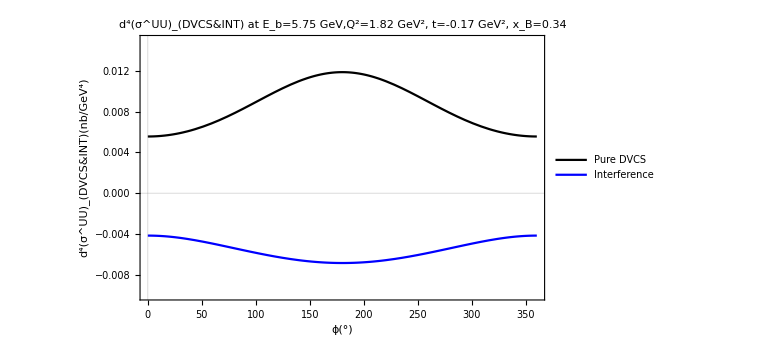

```mathematica
Simplify[{
(((dσDVCS)/.ϕ->ϕp/180*π)/.point1)/.{α->1/2,β->1/2},(((dσINT)/.ϕ->ϕp/180*π)/.point1)/.{α->1/2,β->1/2}
}]
Plot[%,
{ϕp,0,360},
PlotLegends->Placed[LineLegend[{"Pure DVCS","Interference"},
LegendLayout->{"Row",2}],{0.85,0.85}],
ImageSize->Automatic,PlotRange->{Automatic,{-0.01,0.015}},
FrameStyle->Black,FrameLabel->{"ϕ(°)","d^4(σ^UU)_(DVCS&INT)(nb/GeV^4)"},
PlotStyle->{Black,Blue},
PlotLabel->"d^4(σ^UU)_(DVCS&INT) at E_b=5.75 GeV,Q^2=1.82 GeV^2, t=-0.17 GeV^2, x_B=0.34",
PlotRange->All,
PlotTheme -> "Scientific"]
```

{-0.0000317174 (1. Imℰ2T+0.224553 Imℰt2T+0.0575498 Imℋ2T+2.15673 Imℋt2T-0.618967 Reℰ2T+1.23337 Reℰt2T+0.436921 Reℋ2T-0.79004 Reℋt2T) (-4.71552+1. Cos[(π ϕp)/180]) (-0.244666+1. Cos[(π ϕp)/180])+2.15389×10^-7 (1. Imℰ2T^2+6.43528 Imℰt2T^2+56.8188 Imℰt2T Imℋ2T+143.056 Imℋ2T^2+2.94982 Imℋ2T Imℋt2T+3.0923 Imℋt2T^2+Imℰ2T (-2.74457 Imℰt2T-10.8706 Imℋ2T+2.94982 Imℋt2T)+1. Reℰ2T^2-2.74457 Reℰ2T Reℰt2T+6.43528 Reℰt2T^2-10.8706 Reℰ2T Reℋ2T+56.8188 Reℰt2T Reℋ2T+143.056 Reℋ2T^2+2.94982 Reℰ2T Reℋt2T+2.94982 Reℋ2T Reℋt2T+3.0923 Reℋt2T^2) (19.4271-9.43104 Cos[(π ϕp)/180]+1. Cos[(π ϕp)/180]^2),-0.0000318864 (1. Imℰ2T+0.222977 Imℰt2T+0.0603464 Imℋ2T+2.15798 Imℋt2T-0.620581 Reℰ2T+1.23483 Reℰt2T+0.438307 Reℋ2T-0.790498 Reℋt2T) (-4.71552+1. Cos[(π ϕp)/180]) (-0.244666+1. Cos[(π ϕp)/180])+2.08783×10^-7 (1. Imℰ2T^2+6.67374 Imℰt2T^2+58.963 Imℰt2T Imℋ2T+147.516 Imℋ2T^2+2.90374 Imℋ2T Imℋt2T+3.044 Imℋt2T^2+Imℰ2T (-2.84815 Imℰt2T-11.3475 Imℋ2T+2.90374 Imℋt2T)+1. Reℰ2T^2-2.84815 Reℰ2T Reℰt2T+6.67374 Reℰt2T^2-11.3475 Reℰ2T Reℋ2T+58.963 Reℰt2T Reℋ2T+147.516 Reℋ2T^2+2.90374 Reℰ2T Reℋt2T+2.90374 Reℋ2T Reℋt2T+3.044 Reℋt2T^2) (19.4271-9.43104 Cos[(π ϕp)/180]+1. Cos[(π ϕp)/180]^2),-0.0000318864 (1. Imℰ2T+0.222977 Imℰt2T+0.0603464 Imℋ2T+2.15798 Imℋt2T-0.620581 Reℰ2T+1.23483 Reℰt2T+0.438307 Reℋ2T-0.790498 Reℋt2T) (-4.71552+1. Cos[(π ϕp)/180]) (-0.244666+1. Cos[(π ϕp)/180])+2.08783×10^-7 (1. Imℰ2T^2+6.67374 Imℰt2T^2+58.963 Imℰt2T Imℋ2T+147.516 Imℋ2T^2+2.90374 Imℋ2T Imℋt2T+3.044 Imℋt2T^2+Imℰ2T (-2.84815 Imℰt2T-11.3475 Imℋ2T+2.90374 Imℋt2T)+1. Reℰ2T^2-2.84815 Reℰ2T Reℰt2T+6.67374 Reℰt2T^2-11.3475 Reℰ2T Reℋ2T+58.963 Reℰt2T Reℋ2T+147.516 Reℋ2T^2+2.90374 Reℰ2T Reℋt2T+2.90374 Reℋ2T Reℋt2T+3.044 Reℋt2T^2) (19.4271-9.43104 Cos[(π ϕp)/180]+1. Cos[(π ϕp)/180]^2)}

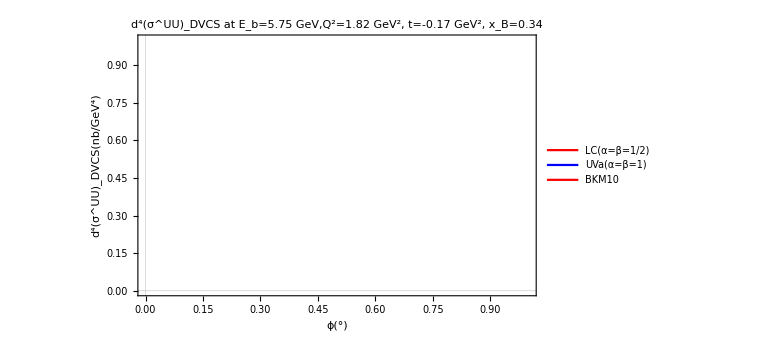

```mathematica
Simplify[
{
(((dσDVCSt3)/.ϕ->ϕp/180*π)/.point1)/.{α->1/2,β->1/2},
(((dσDVCSt3)/.ϕ->ϕp/180*π)/.point1)/.{α->1,β->1},
(((dσDVCSt3)/.ϕ->ϕp/180*π)/.point1)/.{α->1,β->1}
}
]

Plot[%,
{ϕp,0,360},
PlotLegends->Placed[
LineLegend[
{"LC(α=β=1/2)", "UVa(α=β=1)","BKM10"},
LegendLayout->{"Row",3}
],
{0.85,0.85}
],
ImageSize->Automatic,
FrameStyle->Black,
FrameLabel->{"ϕ(°)","d^4(σ^UU)_DVCS(nb/GeV^4)"},
PlotStyle->{Red, Blue},
PlotLabel->"d^4(σ^UU)_DVCS at E_b=5.75 GeV,Q^2=1.82 GeV^2, t=-0.17 GeV^2, x_B=0.34",
PlotTheme -> "Scientific"
]
```

```mathematica
.ϕ->ϕp/180*π
```

{(-0.00646547 Reℰ2T+0.0135349 Reℰt2T+0.000650262 Reℋ2T-0.0128681 Reℋt2T+(0.00599684 Reℰ2T-0.0125006 Reℰt2T-0.00279921 Reℋ2T+0.0117233 Reℋt2T) Cos[(π ϕp)/180]+(0.00939315 Reℰ2T+0.00264453 Reℰt2T-0.0162914 Reℋ2T+0.0172124 Reℋt2T) Cos[(π ϕp)/180]^2+(-0.00224785 Reℰ2T-0.000104284 Reℰt2T+0.00365002 Reℋ2T-0.00414307 Reℋt2T) Cos[(π ϕp)/180]^3+Reℰt2T (-0.0125519+0.00875525 Cos[(π ϕp)/180]-0.00193831 Cos[(π ϕp)/180]^2+0.000137016 Cos[(π ϕp)/180]^3) Pair[Momentum[n],Momentum[p]])/(19.4271-9.43104 Cos[(π ϕp)/180]+1. Cos[(π ϕp)/180]^2),(-0.00644595 Reℰ2T+0.0134848 Reℰt2T+0.0006483 Reℋ2T-0.0128293 Reℋt2T+(0.00597874 Reℰ2T-0.0125346 Reℰt2T-0.00279076 Reℋ2T+0.0116879 Reℋt2T) Cos[(π ϕp)/180]+(0.0093648 Reℰ2T+0.00279975 Reℰt2T-0.0162422 Reℋ2T+0.0171605 Reℋt2T) Cos[(π ϕp)/180]^2+(-0.00224106 Reℰ2T-0.00013529 Reℰt2T+0.003639 Reℋ2T-0.00413057 Reℋt2T) Cos[(π ϕp)/180]^3+Reℰt2T (-0.0125519+0.00875525 Cos[(π ϕp)/180]-0.00193831 Cos[(π ϕp)/180]^2+0.000137016 Cos[(π ϕp)/180]^3) Pair[Momentum[n],Momentum[p]])/(19.4271-9.43104 Cos[(π ϕp)/180]+1. Cos[(π ϕp)/180]^2),(-0.00640807 Reℰ2T+0.0133941 Reℰt2T+0.00064449 Reℋ2T-0.0127539 Reℋt2T+(0.0059436 Reℰ2T-0.0126261 Reℰt2T-0.00277436 Reℋ2T+0.0116192 Reℋt2T) Cos[(π ϕp)/180]+(0.00930976 Reℰ2T+0.00315903 Reℰt2T-0.0161468 Reℋ2T+0.0170596 Reℋt2T) Cos[(π ϕp)/180]^2+(-0.00222789 Reℰ2T-0.000206676 Reℰt2T+0.00361762 Reℋ2T-0.00410629 Reℋt2T) Cos[(π ϕp)/180]^3+Reℰt2T (-0.0125519+0.00875525 Cos[(π ϕp)/180]-0.00193831 Cos[(π ϕp)/180]^2+0.000137016 Cos[(π ϕp)/180]^3) Pair[Momentum[n],Momentum[p]])/(19.4271-9.43104 Cos[(π ϕp)/180]+1. Cos[(π ϕp)/180]^2),(-0.00635068 Reℰ2T+0.0132752 Reℰt2T+0.000638717 Reℋ2T-0.0126396 Reℋt2T+(0.00589037 Reℰ2T-0.0127868 Reℰt2T-0.00274951 Reℋ2T+0.0115151 Reℋt2T) Cos[(π ϕp)/180]+(0.00922637 Reℰ2T+0.00376224 Reℰt2T-0.0160021 Reℋ2T+0.0169068 Reℋt2T) Cos[(π ϕp)/180]^2+(-0.00220794 Reℰ2T-0.000326465 Reℰt2T+0.00358521 Reℋ2T-0.00406951 Reℋt2T) Cos[(π ϕp)/180]^3+Reℰt2T (-0.0125519+0.00875525 Cos[(π ϕp)/180]-0.00193831 Cos[(π ϕp)/180]^2+0.000137016 Cos[(π ϕp)/180]^3) Pair[Momentum[n],Momentum[p]])/(19.4271-9.43104 Cos[(π ϕp)/180]+1. Cos[(π ϕp)/180]^2)}

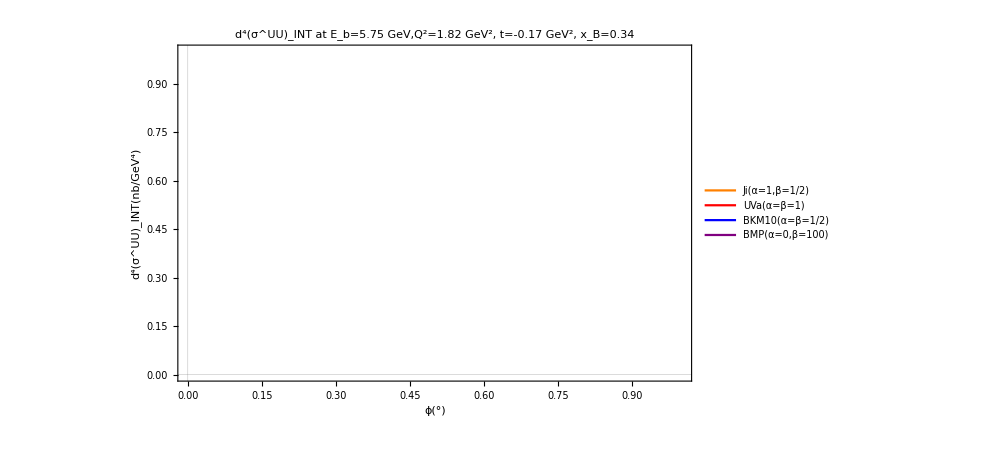

```mathematica
Simplify[
{
(((dσINTt3)/.ϕ->ϕp/180*π)/.point1)/.{α->1,β->1/2},
(((dσINTt3)/.ϕ->ϕp/180*π)/.point1)/.{α->1,β->1},
(((dσINTt3)/.ϕ->ϕp/180*π)/.point1)/.{α->1/2,β->1/2},
(((dσINTt3)/.ϕ->ϕp/180*π)/.point1)/.{α->0,β->100}
}
]

Plot[%,
{ϕp,0,360},
PlotLegends->Placed[
LineLegend[
{"Ji(α=1,β=1/2)","UVa(α=β=1)","BKM10(α=β=1/2)","BMP(α=0,β=100)" },
LegendLayout->{"Row",4}
],
{0.85,0.85}
],
ImageSize->Automatic,
FrameStyle->Black,
FrameLabel->{"ϕ(°)","d^4(σ^UU)_INT(nb/GeV^4)"},
PlotStyle->{Orange,Red, Blue,Purple},
PlotLabel->"d^4(σ^UU)_INT at E_b=5.75 GeV,Q^2=1.82 GeV^2, t=-0.17 GeV^2, x_B=0.34",
PlotRange->{Automatic,{-0.008,0.0}},
PlotTheme -> "Scientific"
]
```